```mathematica
byChromial=Block[{k, result,P, current},
result=Association[];
For[k=1,k≤EndMPG[[9]],k++,
P=Chromial[k];
If[!KeyExistsQ[result,P],
result[P]={k},
current = result[P];
current = Append[current, k];
result[P]=current
]
];
result
];Length[byChromial]
```

```mathematica
byChromial2=Block[{k, result,P, current,count=1},
result=Association[];
For[k=1,k≤EndMPG[[9]],k++,
P=Chromial[k];
If[!KeyExistsQ[result,P],
result[P]=count; count++]
];
result
];Length[byChromial2]
```

502

```mathematica
byChromial2
```

<|-6 x+11 x^2-6 x^3+x^4→1,18 x-39 x^2+29 x^3-9 x^4+x^5→2,-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→3,-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6→4,494,291900 x-1264900 x^2+2452645 x^3-2837585 x^4+2195470 x^5-1202865 x^6+480604 x^7-141632 x^8+30654 x^9-4765 x^10+506 x^11-33 x^12+x^13→499,174072 x-810292 x^2+1692418 x^3-2107529 x^4+1748595 x^5-1020876 x^6+430920 x^7-132756 x^8+29685 x^9-4710 x^10+505 x^11-33 x^12+x^13→500,275322 x-1201549 x^2+2347330 x^3-2736527 x^4+2133349 x^5-1177384 x^6+473611 x^7-140392 x^8+30525 x^9-4759 x^10+506 x^11-33 x^12+x^13→501,175098 x-815419 x^2+1703943 x^3-2122890 x^4+1762035 x^5-1028940 x^6+434280 x^7-133716 x^8+29865 x^9-4730 x^10+506 x^11-33 x^12+x^13→502|>
 |  |  |  |

```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression];Length[deps2]
```

1365053

```mathematica
pol=Block[{k, result,P, Q,record,current, interesting},
result={};
interesting=Select[deps2,
#[[1]]<=EndMPG[[9]]&&#[[2]]<=EndMPG[[9]]&
];
Monitor[
For[k=1,k≤Length[interesting],k++,
record=interesting[[k]];
P=Chromial[record[[1]]];
Q=Chromial[record[[2]]];
result=Append[result,byChromial2[P]->byChromial2[Q]]
],k];
result=DeleteDuplicates[result];
result
]
```

{1→2,2→3,2→4,3→5,3→6,3→7,4→7,5→8,5→9,5→10,6→9,6→11,6→10,7→11,7→12,5→12,8→13,8→14,8→15,9→17,9→16,9→15,9→18,9→19,8→17,10→15,10→16,10→14,10→21,11→18,11→19,11→20,10→18,12→18,12→22,8→22,13→23,13→24,13→25,13→26,14→27,14→24,14→25,14→29,15→27,15→24,15→32,15→30,15→26,14→32,14→28,15→28,16→28,16→31,16→27,16→34,16→33,16→30,17→28,17→36,17→26,17→37,17→38,18→37,18→34,18→39,18→38,18→41,19→38,19→33,19→39,19→34,19→40,15→41,20→39,20→40,20→35,13→36,14→37,21→32,21→34,22→37,22→42,13→42,23→43,23→44,23→45,23→46,24→46,24→50,24→49,24→45,24→48,24→47,24→51,25→44,25→50,25→46,25→57,25→58,25→48,25→47,26→45,26→49,26→57,26→47,26→62,23→62,27→48,27→59,27→61,27→55,27→47,27→51,27→56,24→65,28→47,28→54,28→65,28→49,28→55,28→61,28→60,28→57,27→53,29→61,29→50,29→59,29→58,30→51,30→69,30→49,30→53,30→63,30→54,30→67,30→55,30→61,31→56,31→64,31→63,31→55,31→68,32→59,32→52,32→54,32→70,26→70,24→52,33→54,33→64,33→71,33→67,33→66,33→69,33→72,28→75,28→71,29→60,25→70,34→60,34→64,34→75,34→54,27→75,35→66,35→74,35→73,36→62,36→76,36→57,36→77,36→78,37→60,37→76,37→77,37→79,37→80,28→82,38→54,38→77,38→71,38→79,38→82,38→75,38→81,38→83,26→80,26→83,30→81,39→74,39→64,39→79,39→66,39→69,39→81,39→72,39→82,31→72,34→74,34→84,30→84,40→66,40→74,40→81,40→73,40→72,41→80,41→75,41→69,25→76,23→78,42→76,42→85,23→85,43→86,43→87,43→88,43→89,44→89,44→92,44→86,44→93,44→94,44→91,44→90,45→88,45→92,45→90,45→95,45→102,45→103,45→104,46→89,46→94,46→102,46→91,46→98,46→88,43→103,46→95,46→90,44→104,46→107,46→108,47→108,47→95,47→99,47→100,47→109,47→90,47→92,47→110,47→111,47→96,47→105,47→115,48→91,48→97,48→105,48→90,48→106,48→100,48→101,48→98,48→99,45→122,46→123,47→128,49→95,49→121,49→110,49→127,49→124,49→115,49→125,49→123,49→126,49→105,49→122,50→107,50→121,50→104,50→97,50→94,50→111,50→112,50→130,50→110,50→115,48→125,48→115,47→124,51→98,51→130,51→114,51→126,51→95,51→101,51→99,51→100,51→113,52→135,52→112,52→127,52→138,53→101,53→116,53→133,53→118,53→105,53→114,53→117,53→137,53→110,53→141,51→110,54→138,54→127,54→134,54→116,54→128,54→140,54→136,54→139,54→131,54→121,49→128,49→142,55→99,55→131,55→117,55→134,55→137,55→141,55→124,55→119,55→125,55→126,55→118,56→106,56→132,56→117,56→119,56→99,56→113,56→120,57→92,57→121,57→123,57→125,57→96,57→150,57→151,57→102,58→94,58→97,58→150,58→93,58→152,58→96,44→151,58→111,58→100,59→112,59→131,59→111,59→130,59→132,59→136,60→109,60→121,60→131,60→150,60→153,61→115,61→110,61→117,61→100,61→116,61→139,61→96,62→103,62→123,62→151,62→92,62→157,51→141,43→157,51→160,61→119,61→161,61→160,61→153,48→112,61→136,56→137,54→158,54→161,54→165,63→113,63→140,63→154,63→146,63→126,63→137,63→118,63→119,64→144,64→134,64→164,64→162,64→139,64→163,64→154,64→169,64→140,64→148,64→131,55→139,55→162,65→108,65→109,65→138,65→141,65→102,65→115,53→167,63→166,53→162,55→165,66→166,66→129,66→145,66→155,66→156,66→164,66→159,66→163,66→170,66→158,66→147,63→169,51→138,51→171,59→116,67→142,67→133,67→166,67→116,67→134,67→127,67→162,67→154,68→120,68→148,68→146,68→119,68→118,49→172,53→161,53→173,56→144,51→142,69→171,69→162,69→169,69→167,69→165,69→166,69→172,69→173,69→147,49→171,55→167,68→163,68→164,70→111,70→135,70→128,70→174,67→155,71→139,71→138,71→142,71→144,71→116,71→175,71→129,71→143,71→171,71→167,71→128,62→174,45→135,57→178,57→175,46→135,53→159,72→165,72→163,72→177,72→154,72→170,72→167,72→176,72→164,72→166,72→169,73→156,73→164,73→147,73→168,73→170,73→145,73→155,74→166,74→165,74→164,74→148,74→149,74→129,74→156,74→147,75→109,75→162,75→138,75→144,75→178,75→136,75→181,47→181,44→174,76→182,76→183,76→150,76→184,76→185,57→187,77→175,77→183,77→187,77→178,77→121,77→186,77→182,77→189,78→157,78→184,78→151,78→182,78→191,62→185,62→189,49→190,79→171,79→186,79→188,79→177,79→159,79→187,79→183,79→131,79→149,60→188,80→109,80→185,80→178,80→171,80→192,81→158,81→140,81→186,81→155,81→190,81→167,81→147,81→129,81→165,81→159,81→188,82→139,82→187,82→129,82→158,82→188,82→176,82→190,82→165,82→172,61→188,65→172,47→187,75→165,75→193,74→169,74→188,74→179,74→158,83→128,83→189,83→187,83→181,83→190,51→186,84→169,84→161,84→193,51→193,44→184,43→191,85→184,85→194,43→194,86→195,86→196,86→197,86→198,86→199,86→200,86→206,87→209,87→210,87→198,87→197,88→195,88→206,88→211,88→209,88→212,88→208,88→213,89→200,89→197,89→211,89→196,89→202,89→209,87→212,89→208,89→195,86→213,89→217,89→218,89→214,90→201,90→207,90→203,90→218,90→215,90→195,90→206,90→224,90→221,90→220,90→208,90→219,91→204,91→196,91→215,91→195,91→216,91→201,91→205,91→202,91→203,92→214,92→226,92→207,92→235,92→206,92→236,92→225,92→237,92→211,93→200,93→239,93→204,93→199,93→242,93→207,93→221,94→217,94→235,94→204,94→200,94→245,94→243,94→228,94→213,86→236,93→245,93→201,91→226,91→228,94→225,94→221,93→237,95→220,95→246,95→208,95→214,95→238,95→254,95→256,95→215,95→227,95→251,95→226,90→260,90→255,96→225,96→241,96→219,96→240,96→207,96→239,96→249,96→263,95→224,94→220,94→267,97→228,97→240,97→221,97→244,97→204,97→250,97→252,97→247,97→243,97→241,97→270,98→208,98→205,98→238,98→202,98→243,98→223,98→248,98→272,98→203,98→201,94→219,91→224,94→224,99→276,99→229,99→232,99→275,99→203,99→238,99→226,99→258,99→231,99→277,99→251,99→233,100→201,100→230,100→261,100→232,100→224,100→220,100→207,100→270,98→220,98→222,97→230,101→205,101→230,101→253,101→231,101→215,101→223,101→232,101→233,101→220,101→276,90→283,90→251,102→211,102→235,102→219,102→246,102→285,102→284,102→286,102→287,88→290,103→212,103→236,103→206,103→214,103→285,103→292,103→293,95→225,95→284,95→291,95→255,88→287,104→213,104→237,104→221,104→256,104→286,104→290,104→293,104→255,88→227,98→276,99→266,92→239,92→289,92→286,105→215,105→240,105→230,105→257,105→289,105→261,105→274,105→294,105→255,105→291,105→283,105→266,105→284,105→272,105→288,99→241,99→274,99→296,99→261,89→290,91→289,91→286,106→216,106→244,106→301,106→232,106→222,106→203,106→234,94→260,98→291,100→305,100→250,99→303,98→284,106→233,106→229,89→285,107→290,107→228,107→246,107→248,107→217,107→260,107→272,107→254,108→218,108→267,108→211,108→224,108→276,108→272,108→219,109→314,109→246,109→275,109→235,109→308,109→306,109→263,109→309,101→247,101→274,106→288,90→319,87→292,86→293,100→229,100→321,100→308,100→322,100→249,98→321,110→272,110→254,110→258,110→270,110→261,110→306,110→220,110→225,110→241,110→264,110→318,110→262,110→230,110→255,106→294,90→309,94→256,111→267,111→256,111→277,111→250,111→263,111→260,111→237,111→262,110→257,110→273,95→310,101→313,112→327,112→252,112→257,112→260,112→304,112→273,112→313,112→248,105→311,105→305,113→233,113→231,113→278,113→312,113→222,113→238,113→326,113→295,113→271,113→229,114→223,114→318,114→269,114→295,114→291,114→230,114→258,114→271,114→253,114→296,114→254,115→224,115→263,115→273,115→296,115→286,115→219,115→294,115→319,115→272,115→270,101→296,108→314,110→322,110→303,110→300,113→299,116→313,116→257,116→279,116→240,116→307,116→315,116→325,116→262,116→318,116→305,116→298,116→306,116→273,116→316,116→323,116→297,116→336,117→294,117→258,117→302,117→271,117→335,117→315,117→232,117→261,117→296,117→334,117→307,117→324,117→282,117→241,117→264,118→295,118→259,118→281,118→302,118→317,118→231,118→320,118→324,118→280,118→298,118→332,118→337,118→300,118→266,118→299,113→264,119→229,119→265,119→282,119→328,119→301,119→281,119→295,119→266,119→303,119→299,119→302,120→234,120→268,120→282,120→302,120→231,120→229,120→278,92→345,94→346,95→352,121→344,121→350,121→347,121→263,121→348,121→346,121→349,121→351,121→240,121→345,121→246,99→358,110→361,122→227,122→345,122→255,122→352,122→362,122→319,122→363,122→364,90→362,92→362,103→363,95→364,88→363,99→365,123→214,123→346,123→225,123→344,123→362,123→286,123→369,123→370,123→366,123→289,123→363,124→251,124→347,124→261,124→303,124→357,124→367,124→368,124→362,124→300,124→371,124→364,124→266,98→366,91→369,89→370,107→344,125→226,125→348,125→241,125→350,125→367,125→288,125→366,125→369,125→320,125→362,125→284,125→301,101→320,100→376,124→361,96→347,100→379,110→349,110→381,110→354,126→238,126→351,126→264,126→265,126→303,126→367,126→366,126→300,126→320,126→259,126→274,126→364,126→299,126→266,90→383,95→371,95→384,127→352,127→265,127→361,127→273,127→350,127→344,127→257,95→385,101→311,113→388,114→390,101→391,108→310,128→310,128→352,128→358,128→376,128→394,128→347,128→345,128→379,128→354,128→262,128→383,128→386,128→373,100→394,99→386,129→392,129→353,129→359,129→399,129→377,129→397,129→375,129→378,129→380,129→382,129→298,129→365,129→398,129→374,129→357,129→360,129→373,129→372,129→396,101→395,117→380,107→319,114→393,114→259,114→368,127→381,127→374,115→303,115→384,126→374,126→354,126→390,118→355,118→405,119→359,120→324,104→345,104→327,97→348,97→263,97→277,111→347,111→394,112→350,112→394,130→248,130→351,130→256,130→247,130→277,130→250,130→326,130→318,131→350,131→408,131→316,131→306,131→347,131→265,131→348,131→406,131→351,131→355,131→275,132→304,132→265,132→277,132→326,132→268,132→325,133→311,133→269,133→356,133→279,133→257,133→407,133→318,133→331,133→393,133→334,115→313,115→394,112→275,134→393,134→328,134→279,134→358,134→413,134→325,134→336,134→408,134→265,134→397,134→382,134→361,134→331,134→405,134→350,134→414,105→416,117→279,117→336,117→281,117→325,135→420,135→327,135→352,135→260,135→418,135→419,135→310,123→383,123→421,100→367,98→384,136→394,136→273,136→325,136→336,136→263,136→334,136→424,137→233,137→316,137→271,137→331,137→295,137→335,137→288,137→337,137→324,137→368,137→274,137→302,137→303,99→368,108→371,138→310,138→313,138→374,138→419,138→273,138→393,138→428,138→246,138→427,138→412,138→275,138→394,137→315,137→407,139→412,139→361,139→397,139→307,139→376,139→432,139→407,139→433,139→406,139→354,139→336,139→298,139→426,139→358,139→347,125→376,125→391,119→406,119→335,119→414,119→425,119→300,119→367,113→335,140→312,140→265,140→404,140→315,140→354,140→434,140→336,140→432,140→355,140→406,140→338,140→298,140→413,140→351,141→276,141→306,141→296,141→393,141→274,141→436,141→371,141→295,141→284,141→335,141→303,141→299,106→304,110→424,110→426,101→322,101→436,134→389,134→429,142→385,142→388,142→318,142→421,142→417,142→313,142→361,142→392,142→311,142→358,142→305,142→416,142→391,142→390,142→352,133→332,133→317,143→422,143→305,143→357,143→412,143→430,143→310,143→439,144→440,144→325,144→359,144→412,144→416,144→388,144→312,144→329,144→399,144→336,144→441,144→275,144→442,117→407,145→330,145→341,145→360,145→435,145→343,145→400,145→409,145→382,145→431,145→404,145→438,145→403,145→356,119→336,119→397,146→278,146→338,146→401,146→339,146→302,146→299,146→280,146→259,146→281,146→425,146→337,146→340,130→273,133→333,138→312,147→399,147→410,147→401,147→338,147→411,147→403,147→404,147→353,147→398,147→389,147→360,147→359,147→445,147→437,148→329,148→328,148→343,148→332,148→298,148→342,148→340,148→338,148→336,148→415,148→265,149→386,149→411,149→417,149→265,149→423,149→365,149→377,149→387,118→389,137→399,150→235,150→346,150→348,150→446,150→447,151→236,151→346,151→370,151→369,151→239,151→446,151→448,151→285,96→349,96→447,96→367,131→450,131→449,126→353,93→446,152→245,152→250,152→447,132→316,86→448,130→306,130→424,153→308,153→349,153→406,153→449,153→447,136→450,116→375,154→388,154→331,154→403,154→407,154→390,154→405,154→340,154→332,154→413,154→414,154→336,154→453,154→316,127→454,127→451,124→454,155→317,155→353,155→409,155→404,155→429,155→356,155→452,155→434,155→382,155→403,155→455,155→375,155→360,155→451,126→410,117→456,115→358,99→416,115→412,139→456,139→380,139→458,139→396,117→458,114→459,156→389,156→359,156→400,156→342,156→341,156→401,156→330,156→404,156→382,156→457,156→375,156→402,156→431,156→403,156→343,156→429,156→396,156→360,156→377,146→330,146→460,157→292,157→370,157→448,157→236,157→461,125→378,117→449,119→297,158→373,158→404,158→374,158→382,158→429,158→451,158→462,158→432,158→396,158→455,158→375,158→450,158→297,146→434,148→413,148→464,148→402,148→457,118→432,118→463,87→461,105→358,121→466,121→462,125→466,159→459,159→378,159→356,159→452,159→375,159→458,159→355,159→465,159→398,159→462,159→377,159→372,115→427,115→308,160→321,160→323,160→424,160→335,160→322,160→384,161→379,161→323,161→432,161→427,161→381,161→414,161→456,161→449,161→424,162→416,162→393,162→453,162→467,162→358,162→468,162→414,162→469,162→315,162→334,162→391,162→336,162→390,162→332,162→306,124→358,114→323,114→388,137→468,114→467,163→468,163→380,163→400,163→434,163→457,163→453,163→405,163→442,163→460,163→432,163→342,163→463,137→333,99→412,118→453,91→327,110→462,164→399,164→343,164→397,164→457,164→330,164→464,164→429,164→458,164→453,164→400,164→431,164→450,137→471,162→399,162→471,162→463,154→330,154→460,141→426,141→467,110→472,165→386,165→336,165→455,165→428,165→454,165→359,165→389,165→374,165→466,165→456,165→458,165→397,165→399,165→450,165→453,165→360,165→472,165→469,166→392,166→460,166→332,166→417,166→459,166→468,166→342,166→389,166→403,166→401,166→317,166→397,166→297,166→463,166→333,166→399,166→429,166→330,166→374,167→395,167→315,167→360,167→430,167→390,167→437,167→473,167→388,167→399,167→458,167→432,167→428,167→297,167→456,167→472,167→459,167→380,168→401,168→435,168→402,168→431,168→470,168→403,168→400,168→438,169→441,169→414,169→464,169→471,169→433,169→453,169→342,169→456,169→469,169→432,169→401,170→437,170→470,170→460,170→398,170→431,170→400,170→403,170→438,170→360,170→401,170→455,170→457,164→387,164→340,164→401,164→460,164→359,164→317,164→437,164→389,126→433,126→392,119→399,102→309,102→419,141→428,105→430,105→473,126→459,113→417,146→342,146→464,141→469,124→472,147→463,147→372,147→464,126→469,137→456,113→441,111→305,101→427,95→474,98→419,98→475,99→430,95→439,171→441,171→395,171→472,171→439,171→391,171→476,171→474,171→430,171→459,171→306,171→475,171→386,171→433,171→372,119→468,120→329,114→381,165→357,165→392,165→333,123→477,105→427,105→476,172→474,172→358,172→469,172→472,172→466,172→374,172→426,172→477,172→372,122→474,119→380,124→473,105→379,173→456,173→467,173→476,173→463,101→476,141→388,120→442,123→475,125→395,142→353,174→237,174→418,174→383,174→479,175→376,175→419,175→421,175→440,175→240,175→480,175→365,175→422,175→475,175→395,175→383,114→452,105→378,176→437,176→388,176→407,176→478,176→453,176→397,176→455,176→454,176→468,176→482,176→469,177→398,177→430,177→316,177→481,177→478,177→417,177→442,177→458,177→386,177→441,157→479,103→418,151→483,151→480,88→420,178→309,178→391,178→419,178→440,178→263,178→483,178→484,92→484,89→418,101→465,179→455,179→431,179→445,179→464,180→443,181→314,181→416,181→394,181→484,182→346,182→486,182→487,182→488,182→489,182→480,182→485,182→483,183→348,183→465,183→485,183→491,183→481,183→487,183→475,183→488,183→423,150→491,184→486,184→485,184→446,184→492,184→493,185→483,185→475,185→235,185→493,185→494,151→488,186→452,186→490,186→395,186→411,186→487,186→351,186→462,186→365,186→386,186→465,186→491,187→376,187→365,187→347,187→462,187→488,187→495,187→478,187→491,187→490,187→466,187→378,187→474,187→477,187→496,96→495,102→474,92→496,178→386,178→497,188→433,188→377,188→375,188→466,188→472,188→445,188→462,188→450,188→406,188→491,188→458,188→495,189→383,189→488,189→496,189→484,189→345,189→490,189→489,189→498,123→490,190→354,190→373,190→451,190→490,190→462,190→454,190→499,190→473,190→353,190→466,190→378,191→461,191→492,191→448,191→486,191→500,157→493,157→489,95→490,122→499,115→466,109→472,192→309,192→494,192→439,124→482,100→491,108→477,181→454,181→501,193→424,193→497,193→501,193→469,193→427,193→441,86→492,87→500,194→492,194→502,87→502}

```mathematica
{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85}/.pol
```

{2,3,5,7,8,9,11,13,17,15,18,18,23,27,27,28,28,37,38,39,32,37,43,46,44,45,48,47,61,51,56,59,54,60,66,62,60,54,74,66,80,76,86,89,88,89,108,91,95,107,98,135,101,138,99,106,92,94,112,109,115,103,113,144,108,166,142,120,171,111,139,165,156,166,109,182,175,157,171,109,158,139,128,169,184}

```mathematica
VertexDegree[ Graph[pol, GraphLayout->"RadialDrawing"]]
```

{1,3,4,2,5,4,4,6,7,7,5,4,7,9,10,7,8,9,7,3,4,4,1,3,2,3,3,1,3,2,4,1,4,2,2,4,3,3,2,2,1,2}

```mathematica
FindCycle[Graph[pol],Infinity,All]
```

{}

```mathematica
TreeGraphQ[Graph[pol]]
```

False

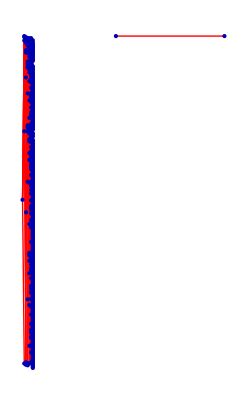

```mathematica
TreePlot[Graph[pol],Left,EdgeRenderingFunction->Function[{p,vl,el},{Red,Line[p]}]]
```

```mathematica
Length[pol]
```

2029

```mathematica
byChromial=Get["d:\\byChromial.txt"]
```

<|-6 x+11 x^2-6 x^3+x^4→1,18 x-39 x^2+29 x^3-9 x^4+x^5→2,-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→3,-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6→4,494,291900 x-1264900 x^2+2452645 x^3-2837585 x^4+2195470 x^5-1202865 x^6+480604 x^7-141632 x^8+30654 x^9-4765 x^10+506 x^11-33 x^12+x^13→499,174072 x-810292 x^2+1692418 x^3-2107529 x^4+1748595 x^5-1020876 x^6+430920 x^7-132756 x^8+29685 x^9-4710 x^10+505 x^11-33 x^12+x^13→500,275322 x-1201549 x^2+2347330 x^3-2736527 x^4+2133349 x^5-1177384 x^6+473611 x^7-140392 x^8+30525 x^9-4759 x^10+506 x^11-33 x^12+x^13→501,175098 x-815419 x^2+1703943 x^3-2122890 x^4+1762035 x^5-1028940 x^6+434280 x^7-133716 x^8+29865 x^9-4730 x^10+506 x^11-33 x^12+x^13→502|>
 |  |  |  |

```mathematica
DecomposePoly[p_]:=Block[
{f,assoc},
f=FactorList[p];
assoc=Association[Map[#[[1]]->#[[2]]&,f]];
{assoc[-1+x],assoc[-2+x],If[KeyExistsQ[assoc,-3+x],assoc[-3+x],0]}
]
```

```mathematica
ExpXMinus3[p_]:=Block[
{f,assoc},
f=FactorList[p];
assoc=Association[Map[#[[1]]->#[[2]]&,f]];
If[KeyExistsQ[assoc,-3+x],assoc[-3+x],0]
]
```

```mathematica
DecomposePoly[(x-1)^10*(x-2)]
```

{10,1,0}

```mathematica
klm=Sort[DeleteDuplicates[Map[DecomposePoly[#]&,Keys[byChromial]]]]
```

{{1,1,0},{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{1,1,10}}

```mathematica
Take[deps2,10]
```

{{1,2,{2,1<->4,2<->3}},{2,3,{2,2<->4,3<->5}},{2,4,{2,2<->5,1<->4}},{3,5,{2,1<->5,2<->3}},{3,6,{2,2<->5,1<->6}},{3,7,{2,3<->5,1<->4}},{3,8,{2,2<->6,3<->5}},{4,7,{2,2<->4,3<->6}},{5,10,{2,3<->4,5<->6}},{5,11,{2,3<->5,4<->7}}}

```mathematica
TableForm[Map[{ExpXMinus3[Chromial[#[[1]]]]-ExpXMinus3[Chromial[#[[2]]]],Chrom[#[[2]]]/24-Chrom[#[[1]]]/24}&,Take[Select[deps2,Chrom[#[[1]]]<Chrom[#[[2]]]&],10]], TableDepth->3]
```

2 | 3
2 | 3
2 | 4
-1 | 1
2 | 4
2 | 3
2 | 3
-1 | 1
1 | 7
2 | 3

```mathematica
TableForm[Map[{FactorList[Chromial[#[[1]]]],FactorList[Chromial[#[[2]]]],Chrom[#[[1]]],Chrom[#[[2]]]}&,Take[Select[deps2,Chrom[#[[1]]]<Chrom[#[[2]]]&],10]], TableDepth->3]
```

{1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1} | {1,1}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | 24 | 96
{1,1}
{-3+x,3}
{-2+x,1}
{-1+x,1}
{x,1} | {1,1}
{-3+x,1}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | 24 | 96
{1,1}
{-3+x,3}
{-2+x,1}
{-1+x,1}
{x,1} | {1,1}
{-3+x,1}
{-2+x,1}
{-1+x,1}
{x,1}
{-35+30 x-9 x^2+x^3,1} | 24 | 120
{1,1}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | {1,1}
{-3+x,1}
{-2+x,1}
{-1+x,1}
{x,1}
{-35+30 x-9 x^2+x^3,1} | 96 | 120
{1,1}
{-3+x,4}
{-2+x,1}
{-1+x,1}
{x,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-35+30 x-9 x^2+x^3,1} | 24 | 120
{1,1}
{-3+x,4}
{-2+x,1}
{-1+x,1}
{x,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | 24 | 96
{1,1}
{-3+x,4}
{-2+x,1}
{-1+x,1}
{x,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | 24 | 96
{1,1}
{-3+x,1}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-35+30 x-9 x^2+x^3,1} | 96 | 120
{1,1}
{-3+x,1}
{-2+x,1}
{-1+x,1}
{x,1}
{-35+30 x-9 x^2+x^3,1} | {1,1}
{-2+x,1}
{-1+x,1}
{x,1}
{-332+498 x-303 x^2+94 x^3-15 x^4+x^5,1} | 120 | 288
{1,1}
{-3+x,4}
{-2+x,1}
{-1+x,1}
{x,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | 24 | 96

```mathematica
TableForm[Map[{FactorList[Chromial[#[[1]]]],FactorList[Chromial[#[[2]]]],Chrom[#[[1]]],Chrom[#[[2]]]}&,Take[Select[deps2,Chrom[#[[1]]]>Chrom[#[[2]]]&],10]], TableDepth->3]
```

{1,1}
{-3+x,1}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | {1,1}
{-3+x,1}
{-2+x,1}
{-1+x,1}
{x,1}
{119-133 x+58 x^2-12 x^3+x^4,1} | 96 | 72
{1,1}
{-3+x,1}
{-2+x,1}
{-1+x,1}
{x,1}
{-35+30 x-9 x^2+x^3,1} | {1,1}
{-3+x,1}
{-2+x,1}
{-1+x,1}
{x,1}
{119-133 x+58 x^2-12 x^3+x^4,1} | 120 | 72
{1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-35+30 x-9 x^2+x^3,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{119-133 x+58 x^2-12 x^3+x^4,1} | 120 | 72
{1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-35+30 x-9 x^2+x^3,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{119-133 x+58 x^2-12 x^3+x^4,1} | 120 | 72
{1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{119-133 x+58 x^2-12 x^3+x^4,1} | 96 | 72
{1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{119-133 x+58 x^2-12 x^3+x^4,1} | 96 | 72
{1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{119-133 x+58 x^2-12 x^3+x^4,1} | 96 | 72
{1,1}
{-3+x,1}
{-2+x,1}
{-1+x,1}
{x,1}
{119-133 x+58 x^2-12 x^3+x^4,1} | {1,1}
{-3+x,1}
{-2+x,1}
{-1+x,1}
{x,1}
{-422+570 x-320 x^2+95 x^3-15 x^4+x^5,1} | 72 | 48
{1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{119-133 x+58 x^2-12 x^3+x^4,1} | 96 | 72
{1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{-32+29 x-9 x^2+x^3,1} | {1,1}
{-3+x,2}
{-2+x,1}
{-1+x,1}
{x,1}
{119-133 x+58 x^2-12 x^3+x^4,1} | 96 | 72

```mathematica
Select[Sort[DeleteDuplicates[Map[Last[FactorList[#]][[1]]&,Keys[byChromial]]]],Exponent[#,x]==9&]
```

{-45860+115520 x-131190 x^2+88471 x^3-39164 x^4+11829 x^5-2441 x^6+332 x^7-27 x^8+x^9,-41108+106556 x-124125 x^2+85487 x^3-38450 x^4+11737 x^5-2436 x^6+332 x^7-27 x^8+x^9,-36212+96992 x-116339 x^2+82102 x^3-37620 x^4+11628 x^5-2430 x^6+332 x^7-27 x^8+x^9,-29012+81860 x-102981 x^2+75761 x^3-35913 x^4+11381 x^5-2415 x^6+332 x^7-27 x^8+x^9,-68578+154656 x-159801 x^2+100000 x^3-41933 x^4+12225 x^5-2472 x^6+333 x^7-27 x^8+x^9,-62858+145762 x-154151 x^2+98134 x^3-41599 x^4+12195 x^5-2471 x^6+333 x^7-27 x^8+x^9,-63452+146653 x-154673 x^2+98282 x^3-41619 x^4+12196 x^5-2471 x^6+333 x^7-27 x^8+x^9,-64430+148170 x-155619 x^2+98579 x^3-41666 x^4+12199 x^5-2471 x^6+333 x^7-27 x^8+x^9,-65033+149103 x-156202 x^2+98764 x^3-41696 x^4+12201 x^5-2471 x^6+333 x^7-27 x^8+x^9,-59243+139949 x-150320 x^2+96811 x^3-41347 x^4+12170 x^5-2470 x^6+333 x^7-27 x^8+x^9,-60233+141509 x-151300 x^2+97118 x^3-41395 x^4+12173 x^5-2470 x^6+333 x^7-27 x^8+x^9,-60845+142475 x-151911 x^2+97312 x^3-41426 x^4+12175 x^5-2470 x^6+333 x^7-27 x^8+x^9,-61817+143960 x-152802 x^2+97573 x^3-41463 x^4+12177 x^5-2470 x^6+333 x^7-27 x^8+x^9,-61832+144025 x-152885 x^2+97618 x^3-41474 x^4+12178 x^5-2470 x^6+333 x^7-27 x^8+x^9,-62438+144968 x-153474 x^2+97804 x^3-41504 x^4+12180 x^5-2470 x^6+333 x^7-27 x^8+x^9,-62813+145552 x-153837 x^2+97916 x^3-41521 x^4+12181 x^5-2470 x^6+333 x^7-27 x^8+x^9,-63422+146508 x-154442 x^2+98109 x^3-41552 x^4+12183 x^5-2470 x^6+333 x^7-27 x^8+x^9,-64400+148025 x-155388 x^2+98406 x^3-41599 x^4+12186 x^5-2470 x^6+333 x^7-27 x^8+x^9,-56573+135522 x-147296 x^2+95722 x^3-41129 x^4+12147 x^5-2469 x^6+333 x^7-27 x^8+x^9,-57572+137115 x-148304 x^2+96038 x^3-41178 x^4+12150 x^5-2469 x^6+333 x^7-27 x^8+x^9,-58580+138750 x-149373 x^2+96391 x^3-41237 x^4+12154 x^5-2469 x^6+333 x^7-27 x^8+x^9,-59183+139674 x-149923 x^2+96548 x^3-41258 x^4+12155 x^5-2469 x^6+333 x^7-27 x^8+x^9,-59198+139739 x-150006 x^2+96593 x^3-41269 x^4+12156 x^5-2469 x^6+333 x^7-27 x^8+x^9,-60173+141234 x-150903 x^2+96855 x^3-41306 x^4+12158 x^5-2469 x^6+333 x^7-27 x^8+x^9,-60203+141364 x-151069 x^2+96945 x^3-41328 x^4+12160 x^5-2469 x^6+333 x^7-27 x^8+x^9,-60800+142265 x-151597 x^2+97094 x^3-41348 x^4+12161 x^5-2469 x^6+333 x^7-27 x^8+x^9,-61172+142836 x-151944 x^2+97199 x^3-41364 x^4+12162 x^5-2469 x^6+333 x^7-27 x^8+x^9,-54890+132645 x-145246 x^2+94939 x^3-40959 x^4+12127 x^5-2468 x^6+333 x^7-27 x^8+x^9,-55907+134313 x-146343 x^2+95301 x^3-41019 x^4+12131 x^5-2468 x^6+333 x^7-27 x^8+x^9,-56513+135247 x-146899 x^2+95459 x^3-41040 x^4+12132 x^5-2468 x^6+333 x^7-27 x^8+x^9,-56528+135312 x-146982 x^2+95504 x^3-41051 x^4+12133 x^5-2468 x^6+333 x^7-27 x^8+x^9,-57512+136840 x-147907 x^2+95775 x^3-41089 x^4+12135 x^5-2468 x^6+333 x^7-27 x^8+x^9,-57527+136905 x-147990 x^2+95820 x^3-41100 x^4+12136 x^5-2468 x^6+333 x^7-27 x^8+x^9,-57542+136970 x-148073 x^2+95865 x^3-41111 x^4+12137 x^5-2468 x^6+333 x^7-27 x^8+x^9,-58142+137881 x-148607 x^2+96015 x^3-41131 x^4+12138 x^5-2468 x^6+333 x^7-27 x^8+x^9,-58535+138540 x-149059 x^2+96173 x^3-41159 x^4+12140 x^5-2468 x^6+333 x^7-27 x^8+x^9,-58172+138011 x-148773 x^2+96105 x^3-41153 x^4+12140 x^5-2468 x^6+333 x^7-27 x^8+x^9,-59522+140087 x-150023 x^2+96473 x^3-41206 x^4+12143 x^5-2468 x^6+333 x^7-27 x^8+x^9,-59762+140482 x-150287 x^2+96562 x^3-41221 x^4+12144 x^5-2468 x^6+333 x^7-27 x^8+x^9,-53183+129670 x-143085 x^2+94102 x^3-40777 x^4+12106 x^5-2467 x^6+333 x^7-27 x^8+x^9,-53822+130744 x-143813 x^2+94351 x^3-40820 x^4+12109 x^5-2467 x^6+333 x^7-27 x^8+x^9,-54830+132370 x-144849 x^2+94676 x^3-40870 x^4+12112 x^5-2467 x^6+333 x^7-27 x^8+x^9,-54845+132435 x-144932 x^2+94721 x^3-40881 x^4+12113 x^5-2467 x^6+333 x^7-27 x^8+x^9,-55832+133973 x-145863 x^2+94993 x^3-40919 x^4+12115 x^5-2467 x^6+333 x^7-27 x^8+x^9,-55847+134038 x-145946 x^2+95038 x^3-40930 x^4+12116 x^5-2467 x^6+333 x^7-27 x^8+x^9,-55478+133486 x-145638 x^2+94962 x^3-40923 x^4+12116 x^5-2467 x^6+333 x^7-27 x^8+x^9,-56468+135037 x-146585 x^2+95241 x^3-40962 x^4+12118 x^5-2467 x^6+333 x^7-27 x^8+x^9,-56858+135683 x-147021 x^2+95392 x^3-40989 x^4+12120 x^5-2467 x^6+333 x^7-27 x^8+x^9,-57095+136065 x-147269 x^2+95474 x^3-41003 x^4+12121 x^5-2467 x^6+333 x^7-27 x^8+x^9,-52112+127759 x-141646 x^2+93513 x^3-40638 x^4+12088 x^5-2466 x^6+333 x^7-27 x^8+x^9,-53138+129460 x-142771 x^2+93884 x^3-40699 x^4+12092 x^5-2466 x^6+333 x^7-27 x^8+x^9,-53762+130469 x-143416 x^2+94088 x^3-40731 x^4+12094 x^5-2466 x^6+333 x^7-27 x^8+x^9,-54158+131138 x-143874 x^2+94247 x^3-40759 x^4+12096 x^5-2466 x^6+333 x^7-27 x^8+x^9,-53792+130599 x-143582 x^2+94178 x^3-40753 x^4+12096 x^5-2466 x^6+333 x^7-27 x^8+x^9,-54800+132225 x-144618 x^2+94503 x^3-40803 x^4+12099 x^5-2466 x^6+333 x^7-27 x^8+x^9,-55403+133146 x-145158 x^2+94654 x^3-40823 x^4+12100 x^5-2466 x^6+333 x^7-27 x^8+x^9,-55172+132793 x-144955 x^2+94602 x^3-40818 x^4+12100 x^5-2466 x^6+333 x^7-27 x^8+x^9,-50378+124676 x-139368 x^2+92621 x^3-40444 x^4+12066 x^5-2465 x^6+333 x^7-27 x^8+x^9,-50393+124741 x-139451 x^2+92666 x^3-40455 x^4+12067 x^5-2465 x^6+333 x^7-27 x^8+x^9,-51422+126452 x-140582 x^2+93038 x^3-40516 x^4+12071 x^5-2465 x^6+333 x^7-27 x^8+x^9,-51437+126517 x-140665 x^2+93083 x^3-40527 x^4+12072 x^5-2465 x^6+333 x^7-27 x^8+x^9,-52052+127484 x-141249 x^2+93250 x^3-40549 x^4+12073 x^5-2465 x^6+333 x^7-27 x^8+x^9,-53078+129185 x-142374 x^2+93621 x^3-40610 x^4+12077 x^5-2465 x^6+333 x^7-27 x^8+x^9,-52703+128610 x-142044 x^2+93537 x^3-40602 x^4+12077 x^5-2465 x^6+333 x^7-27 x^8+x^9,-53093+129250 x-142457 x^2+93666 x^3-40621 x^4+12078 x^5-2465 x^6+333 x^7-27 x^8+x^9,-53702+130194 x-143019 x^2+93825 x^3-40642 x^4+12079 x^5-2465 x^6+333 x^7-27 x^8+x^9,-54113+130928 x-143560 x^2+94029 x^3-40681 x^4+12082 x^5-2465 x^6+333 x^7-27 x^8+x^9,-54347+131297 x-143792 x^2+94104 x^3-40694 x^4+12083 x^5-2465 x^6+333 x^7-27 x^8+x^9,-48650+121625 x-137145 x^2+91765 x^3-40260 x^4+12045 x^5-2464 x^6+333 x^7-27 x^8+x^9,-49298+122732 x-137901 x^2+92023 x^3-40304 x^4+12048 x^5-2464 x^6+333 x^7-27 x^8+x^9,-50975+125550 x-139788 x^2+92653 x^3-40409 x^4+12055 x^5-2464 x^6+333 x^7-27 x^8+x^9,-50990+125615 x-139871 x^2+92698 x^3-40420 x^4+12056 x^5-2464 x^6+333 x^7-27 x^8+x^9,-51992+127209 x-140852 x^2+92987 x^3-40460 x^4+12058 x^5-2464 x^6+333 x^7-27 x^8+x^9,-51982+127169 x-140810 x^2+92971 x^3-40458 x^4+12058 x^5-2464 x^6+333 x^7-27 x^8+x^9,-52400+127930 x-141377 x^2+93184 x^3-40498 x^4+12061 x^5-2464 x^6+333 x^7-27 x^8+x^9,-52658+128400 x-141730 x^2+93319 x^3-40524 x^4+12063 x^5-2464 x^6+333 x^7-27 x^8+x^9,-47552+119606 x-135589 x^2+91121 x^3-40109 x^4+12026 x^5-2463 x^6+333 x^7-27 x^8+x^9,-49652+123201 x-138051 x^2+91965 x^3-40254 x^4+12036 x^5-2463 x^6+333 x^7-27 x^8+x^9,-50288+124256 x-138740 x^2+92185 x^3-40288 x^4+12038 x^5-2463 x^6+333 x^7-27 x^8+x^9,-50678+124899 x-139166 x^2+92330 x^3-40314 x^4+12040 x^5-2463 x^6+333 x^7-27 x^8+x^9,-50708+125029 x-139332 x^2+92420 x^3-40336 x^4+12042 x^5-2463 x^6+333 x^7-27 x^8+x^9,-51563+126388 x-140170 x^2+92670 x^3-40372 x^4+12044 x^5-2463 x^6+333 x^7-27 x^8+x^9,-48182+120620 x-136181 x^2+91244 x^3-40096 x^4+12017 x^5-2462 x^6+333 x^7-27 x^8+x^9,-49178+122182 x-137107 x^2+91497 x^3-40126 x^4+12018 x^5-2462 x^6+333 x^7-27 x^8+x^9,-49592+122926 x-137654 x^2+91702 x^3-40165 x^4+12021 x^5-2462 x^6+333 x^7-27 x^8+x^9,-50218+123941 x-138301 x^2+91906 x^3-40197 x^4+12023 x^5-2462 x^6+333 x^7-27 x^8+x^9,-49847+123383 x-137991 x^2+91830 x^3-40190 x^4+12023 x^5-2462 x^6+333 x^7-27 x^8+x^9,-45752+116237 x-132935 x^2+89992 x^3-39835 x^4+11990 x^5-2461 x^6+333 x^7-27 x^8+x^9,-46403+117354 x-133697 x^2+90251 x^3-39879 x^4+11993 x^5-2461 x^6+333 x^7-27 x^8+x^9,-46808+118056 x-134183 x^2+90419 x^3-39908 x^4+11995 x^5-2461 x^6+333 x^7-27 x^8+x^9,-47888+119982 x-135575 x^2+90928 x^3-40002 x^4+12002 x^5-2461 x^6+333 x^7-27 x^8+x^9,-49138+121997 x-136834 x^2+91308 x^3-40057 x^4+12005 x^5-2461 x^6+333 x^7-27 x^8+x^9,-48763+121423 x-136507 x^2+91225 x^3-40049 x^4+12005 x^5-2461 x^6+333 x^7-27 x^8+x^9,-44630+114120 x-131268 x^2+89294 x^3-39672 x^4+11970 x^5-2460 x^6+333 x^7-27 x^8+x^9,-46358+117144 x-133383 x^2+90033 x^3-39801 x^4+11979 x^5-2460 x^6+333 x^7-27 x^8+x^9,-47798+119577 x-135012 x^2+90575 x^3-39891 x^4+11985 x^5-2460 x^6+333 x^7-27 x^8+x^9,-43928+112770 x-130170 x^2+88809 x^3-39549 x^4+11953 x^5-2459 x^6+333 x^7-27 x^8+x^9,-45263+115144 x-131866 x^2+89418 x^3-39659 x^4+11961 x^5-2459 x^6+333 x^7-27 x^8+x^9,-46070+116535 x-132822 x^2+89747 x^3-39716 x^4+11965 x^5-2459 x^6+333 x^7-27 x^8+x^9,-46955+118015 x-133793 x^2+90059 x^3-39765 x^4+11968 x^5-2459 x^6+333 x^7-27 x^8+x^9,-44942+114389 x-131110 x^2+89019 x^3-39544 x^4+11944 x^5-2458 x^6+333 x^7-27 x^8+x^9,-45203+114869 x-131469 x^2+89155 x^3-39570 x^4+11946 x^5-2458 x^6+333 x^7-27 x^8+x^9,-45887+116132 x-132426 x^2+89527 x^3-39644 x^4+11952 x^5-2458 x^6+333 x^7-27 x^8+x^9,-41642+108348 x-126571 x^2+87230 x^3-39155 x^4+11900 x^5-2456 x^6+333 x^7-27 x^8+x^9,-43142+111029 x-128489 x^2+87918 x^3-39279 x^4+11909 x^5-2456 x^6+333 x^7-27 x^8+x^9,-44047+112591 x-129554 x^2+88277 x^3-39339 x^4+11913 x^5-2456 x^6+333 x^7-27 x^8+x^9,-42263+109317 x-127092 x^2+87310 x^3-39131 x^4+11890 x^5-2455 x^6+333 x^7-27 x^8+x^9,-42955+110610 x-128076 x^2+87691 x^3-39206 x^4+11896 x^5-2455 x^6+333 x^7-27 x^8+x^9,-41318+107571 x-125757 x^2+86763 x^3-39002 x^4+11873 x^5-2454 x^6+333 x^7-27 x^8+x^9,-39062+103315 x-122474 x^2+85452 x^3-38722 x^4+11844 x^5-2453 x^6+333 x^7-27 x^8+x^9,-41123+107116 x-125294 x^2+86505 x^3-38920 x^4+11859 x^5-2453 x^6+333 x^7-27 x^8+x^9,-38603+102370 x-121646 x^2+85057 x^3-38614 x^4+11828 x^5-2452 x^6+333 x^7-27 x^8+x^9,-37118+99319 x-118991 x^2+83805 x^3-38277 x^4+11779 x^5-2449 x^6+333 x^7-27 x^8+x^9,-38083+101135 x-120368 x^2+84332 x^3-38379 x^4+11787 x^5-2449 x^6+333 x^7-27 x^8+x^9,-36903+98768 x-118375 x^2+83428 x^3-38145 x^4+11754 x^5-2447 x^6+333 x^7-27 x^8+x^9,-34223+93302 x-113713 x^2+81305 x^3-37603 x^4+11681 x^5-2443 x^6+333 x^7-27 x^8+x^9,-29183+82401 x-103739 x^2+76362 x^3-36203 x^4+11466 x^5-2429 x^6+333 x^7-27 x^8+x^9}

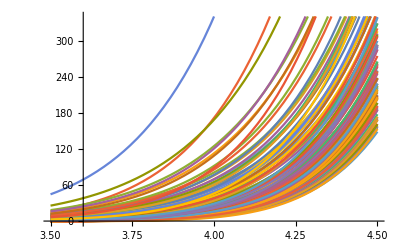

```mathematica
Plot[{-45860+115520 x-131190 x^2+88471 x^3-39164 x^4+11829 x^5-2441 x^6+332 x^7-27 x^8+x^9,-41108+106556 x-124125 x^2+85487 x^3-38450 x^4+11737 x^5-2436 x^6+332 x^7-27 x^8+x^9,-36212+96992 x-116339 x^2+82102 x^3-37620 x^4+11628 x^5-2430 x^6+332 x^7-27 x^8+x^9,-29012+81860 x-102981 x^2+75761 x^3-35913 x^4+11381 x^5-2415 x^6+332 x^7-27 x^8+x^9,-68578+154656 x-159801 x^2+100000 x^3-41933 x^4+12225 x^5-2472 x^6+333 x^7-27 x^8+x^9,-62858+145762 x-154151 x^2+98134 x^3-41599 x^4+12195 x^5-2471 x^6+333 x^7-27 x^8+x^9,-63452+146653 x-154673 x^2+98282 x^3-41619 x^4+12196 x^5-2471 x^6+333 x^7-27 x^8+x^9,-64430+148170 x-155619 x^2+98579 x^3-41666 x^4+12199 x^5-2471 x^6+333 x^7-27 x^8+x^9,-65033+149103 x-156202 x^2+98764 x^3-41696 x^4+12201 x^5-2471 x^6+333 x^7-27 x^8+x^9,-59243+139949 x-150320 x^2+96811 x^3-41347 x^4+12170 x^5-2470 x^6+333 x^7-27 x^8+x^9,-60233+141509 x-151300 x^2+97118 x^3-41395 x^4+12173 x^5-2470 x^6+333 x^7-27 x^8+x^9,-60845+142475 x-151911 x^2+97312 x^3-41426 x^4+12175 x^5-2470 x^6+333 x^7-27 x^8+x^9,-61817+143960 x-152802 x^2+97573 x^3-41463 x^4+12177 x^5-2470 x^6+333 x^7-27 x^8+x^9,-61832+144025 x-152885 x^2+97618 x^3-41474 x^4+12178 x^5-2470 x^6+333 x^7-27 x^8+x^9,-62438+144968 x-153474 x^2+97804 x^3-41504 x^4+12180 x^5-2470 x^6+333 x^7-27 x^8+x^9,-62813+145552 x-153837 x^2+97916 x^3-41521 x^4+12181 x^5-2470 x^6+333 x^7-27 x^8+x^9,-63422+146508 x-154442 x^2+98109 x^3-41552 x^4+12183 x^5-2470 x^6+333 x^7-27 x^8+x^9,-64400+148025 x-155388 x^2+98406 x^3-41599 x^4+12186 x^5-2470 x^6+333 x^7-27 x^8+x^9,-56573+135522 x-147296 x^2+95722 x^3-41129 x^4+12147 x^5-2469 x^6+333 x^7-27 x^8+x^9,-57572+137115 x-148304 x^2+96038 x^3-41178 x^4+12150 x^5-2469 x^6+333 x^7-27 x^8+x^9,-58580+138750 x-149373 x^2+96391 x^3-41237 x^4+12154 x^5-2469 x^6+333 x^7-27 x^8+x^9,-59183+139674 x-149923 x^2+96548 x^3-41258 x^4+12155 x^5-2469 x^6+333 x^7-27 x^8+x^9,-59198+139739 x-150006 x^2+96593 x^3-41269 x^4+12156 x^5-2469 x^6+333 x^7-27 x^8+x^9,-60173+141234 x-150903 x^2+96855 x^3-41306 x^4+12158 x^5-2469 x^6+333 x^7-27 x^8+x^9,-60203+141364 x-151069 x^2+96945 x^3-41328 x^4+12160 x^5-2469 x^6+333 x^7-27 x^8+x^9,-60800+142265 x-151597 x^2+97094 x^3-41348 x^4+12161 x^5-2469 x^6+333 x^7-27 x^8+x^9,-61172+142836 x-151944 x^2+97199 x^3-41364 x^4+12162 x^5-2469 x^6+333 x^7-27 x^8+x^9,-54890+132645 x-145246 x^2+94939 x^3-40959 x^4+12127 x^5-2468 x^6+333 x^7-27 x^8+x^9,-55907+134313 x-146343 x^2+95301 x^3-41019 x^4+12131 x^5-2468 x^6+333 x^7-27 x^8+x^9,-56513+135247 x-146899 x^2+95459 x^3-41040 x^4+12132 x^5-2468 x^6+333 x^7-27 x^8+x^9,-56528+135312 x-146982 x^2+95504 x^3-41051 x^4+12133 x^5-2468 x^6+333 x^7-27 x^8+x^9,-57512+136840 x-147907 x^2+95775 x^3-41089 x^4+12135 x^5-2468 x^6+333 x^7-27 x^8+x^9,-57527+136905 x-147990 x^2+95820 x^3-41100 x^4+12136 x^5-2468 x^6+333 x^7-27 x^8+x^9,-57542+136970 x-148073 x^2+95865 x^3-41111 x^4+12137 x^5-2468 x^6+333 x^7-27 x^8+x^9,-58142+137881 x-148607 x^2+96015 x^3-41131 x^4+12138 x^5-2468 x^6+333 x^7-27 x^8+x^9,-58535+138540 x-149059 x^2+96173 x^3-41159 x^4+12140 x^5-2468 x^6+333 x^7-27 x^8+x^9,-58172+138011 x-148773 x^2+96105 x^3-41153 x^4+12140 x^5-2468 x^6+333 x^7-27 x^8+x^9,-59522+140087 x-150023 x^2+96473 x^3-41206 x^4+12143 x^5-2468 x^6+333 x^7-27 x^8+x^9,-59762+140482 x-150287 x^2+96562 x^3-41221 x^4+12144 x^5-2468 x^6+333 x^7-27 x^8+x^9,-53183+129670 x-143085 x^2+94102 x^3-40777 x^4+12106 x^5-2467 x^6+333 x^7-27 x^8+x^9,-53822+130744 x-143813 x^2+94351 x^3-40820 x^4+12109 x^5-2467 x^6+333 x^7-27 x^8+x^9,-54830+132370 x-144849 x^2+94676 x^3-40870 x^4+12112 x^5-2467 x^6+333 x^7-27 x^8+x^9,-54845+132435 x-144932 x^2+94721 x^3-40881 x^4+12113 x^5-2467 x^6+333 x^7-27 x^8+x^9,-55832+133973 x-145863 x^2+94993 x^3-40919 x^4+12115 x^5-2467 x^6+333 x^7-27 x^8+x^9,-55847+134038 x-145946 x^2+95038 x^3-40930 x^4+12116 x^5-2467 x^6+333 x^7-27 x^8+x^9,-55478+133486 x-145638 x^2+94962 x^3-40923 x^4+12116 x^5-2467 x^6+333 x^7-27 x^8+x^9,-56468+135037 x-146585 x^2+95241 x^3-40962 x^4+12118 x^5-2467 x^6+333 x^7-27 x^8+x^9,-56858+135683 x-147021 x^2+95392 x^3-40989 x^4+12120 x^5-2467 x^6+333 x^7-27 x^8+x^9,-57095+136065 x-147269 x^2+95474 x^3-41003 x^4+12121 x^5-2467 x^6+333 x^7-27 x^8+x^9,-52112+127759 x-141646 x^2+93513 x^3-40638 x^4+12088 x^5-2466 x^6+333 x^7-27 x^8+x^9,-53138+129460 x-142771 x^2+93884 x^3-40699 x^4+12092 x^5-2466 x^6+333 x^7-27 x^8+x^9,-53762+130469 x-143416 x^2+94088 x^3-40731 x^4+12094 x^5-2466 x^6+333 x^7-27 x^8+x^9,-54158+131138 x-143874 x^2+94247 x^3-40759 x^4+12096 x^5-2466 x^6+333 x^7-27 x^8+x^9,-53792+130599 x-143582 x^2+94178 x^3-40753 x^4+12096 x^5-2466 x^6+333 x^7-27 x^8+x^9,-54800+132225 x-144618 x^2+94503 x^3-40803 x^4+12099 x^5-2466 x^6+333 x^7-27 x^8+x^9,-55403+133146 x-145158 x^2+94654 x^3-40823 x^4+12100 x^5-2466 x^6+333 x^7-27 x^8+x^9,-55172+132793 x-144955 x^2+94602 x^3-40818 x^4+12100 x^5-2466 x^6+333 x^7-27 x^8+x^9,-50378+124676 x-139368 x^2+92621 x^3-40444 x^4+12066 x^5-2465 x^6+333 x^7-27 x^8+x^9,-50393+124741 x-139451 x^2+92666 x^3-40455 x^4+12067 x^5-2465 x^6+333 x^7-27 x^8+x^9,-51422+126452 x-140582 x^2+93038 x^3-40516 x^4+12071 x^5-2465 x^6+333 x^7-27 x^8+x^9,-51437+126517 x-140665 x^2+93083 x^3-40527 x^4+12072 x^5-2465 x^6+333 x^7-27 x^8+x^9,-52052+127484 x-141249 x^2+93250 x^3-40549 x^4+12073 x^5-2465 x^6+333 x^7-27 x^8+x^9,-53078+129185 x-142374 x^2+93621 x^3-40610 x^4+12077 x^5-2465 x^6+333 x^7-27 x^8+x^9,-52703+128610 x-142044 x^2+93537 x^3-40602 x^4+12077 x^5-2465 x^6+333 x^7-27 x^8+x^9,-53093+129250 x-142457 x^2+93666 x^3-40621 x^4+12078 x^5-2465 x^6+333 x^7-27 x^8+x^9,-53702+130194 x-143019 x^2+93825 x^3-40642 x^4+12079 x^5-2465 x^6+333 x^7-27 x^8+x^9,-54113+130928 x-143560 x^2+94029 x^3-40681 x^4+12082 x^5-2465 x^6+333 x^7-27 x^8+x^9,-54347+131297 x-143792 x^2+94104 x^3-40694 x^4+12083 x^5-2465 x^6+333 x^7-27 x^8+x^9,-48650+121625 x-137145 x^2+91765 x^3-40260 x^4+12045 x^5-2464 x^6+333 x^7-27 x^8+x^9,-49298+122732 x-137901 x^2+92023 x^3-40304 x^4+12048 x^5-2464 x^6+333 x^7-27 x^8+x^9,-50975+125550 x-139788 x^2+92653 x^3-40409 x^4+12055 x^5-2464 x^6+333 x^7-27 x^8+x^9,-50990+125615 x-139871 x^2+92698 x^3-40420 x^4+12056 x^5-2464 x^6+333 x^7-27 x^8+x^9,-51992+127209 x-140852 x^2+92987 x^3-40460 x^4+12058 x^5-2464 x^6+333 x^7-27 x^8+x^9,-51982+127169 x-140810 x^2+92971 x^3-40458 x^4+12058 x^5-2464 x^6+333 x^7-27 x^8+x^9,-52400+127930 x-141377 x^2+93184 x^3-40498 x^4+12061 x^5-2464 x^6+333 x^7-27 x^8+x^9,-52658+128400 x-141730 x^2+93319 x^3-40524 x^4+12063 x^5-2464 x^6+333 x^7-27 x^8+x^9,-47552+119606 x-135589 x^2+91121 x^3-40109 x^4+12026 x^5-2463 x^6+333 x^7-27 x^8+x^9,-49652+123201 x-138051 x^2+91965 x^3-40254 x^4+12036 x^5-2463 x^6+333 x^7-27 x^8+x^9,-50288+124256 x-138740 x^2+92185 x^3-40288 x^4+12038 x^5-2463 x^6+333 x^7-27 x^8+x^9,-50678+124899 x-139166 x^2+92330 x^3-40314 x^4+12040 x^5-2463 x^6+333 x^7-27 x^8+x^9,-50708+125029 x-139332 x^2+92420 x^3-40336 x^4+12042 x^5-2463 x^6+333 x^7-27 x^8+x^9,-51563+126388 x-140170 x^2+92670 x^3-40372 x^4+12044 x^5-2463 x^6+333 x^7-27 x^8+x^9,-48182+120620 x-136181 x^2+91244 x^3-40096 x^4+12017 x^5-2462 x^6+333 x^7-27 x^8+x^9,-49178+122182 x-137107 x^2+91497 x^3-40126 x^4+12018 x^5-2462 x^6+333 x^7-27 x^8+x^9,-49592+122926 x-137654 x^2+91702 x^3-40165 x^4+12021 x^5-2462 x^6+333 x^7-27 x^8+x^9,-50218+123941 x-138301 x^2+91906 x^3-40197 x^4+12023 x^5-2462 x^6+333 x^7-27 x^8+x^9,-49847+123383 x-137991 x^2+91830 x^3-40190 x^4+12023 x^5-2462 x^6+333 x^7-27 x^8+x^9,-45752+116237 x-132935 x^2+89992 x^3-39835 x^4+11990 x^5-2461 x^6+333 x^7-27 x^8+x^9,-46403+117354 x-133697 x^2+90251 x^3-39879 x^4+11993 x^5-2461 x^6+333 x^7-27 x^8+x^9,-46808+118056 x-134183 x^2+90419 x^3-39908 x^4+11995 x^5-2461 x^6+333 x^7-27 x^8+x^9,-47888+119982 x-135575 x^2+90928 x^3-40002 x^4+12002 x^5-2461 x^6+333 x^7-27 x^8+x^9,-49138+121997 x-136834 x^2+91308 x^3-40057 x^4+12005 x^5-2461 x^6+333 x^7-27 x^8+x^9,-48763+121423 x-136507 x^2+91225 x^3-40049 x^4+12005 x^5-2461 x^6+333 x^7-27 x^8+x^9,-44630+114120 x-131268 x^2+89294 x^3-39672 x^4+11970 x^5-2460 x^6+333 x^7-27 x^8+x^9,-46358+117144 x-133383 x^2+90033 x^3-39801 x^4+11979 x^5-2460 x^6+333 x^7-27 x^8+x^9,-47798+119577 x-135012 x^2+90575 x^3-39891 x^4+11985 x^5-2460 x^6+333 x^7-27 x^8+x^9,-43928+112770 x-130170 x^2+88809 x^3-39549 x^4+11953 x^5-2459 x^6+333 x^7-27 x^8+x^9,-45263+115144 x-131866 x^2+89418 x^3-39659 x^4+11961 x^5-2459 x^6+333 x^7-27 x^8+x^9,-46070+116535 x-132822 x^2+89747 x^3-39716 x^4+11965 x^5-2459 x^6+333 x^7-27 x^8+x^9,-46955+118015 x-133793 x^2+90059 x^3-39765 x^4+11968 x^5-2459 x^6+333 x^7-27 x^8+x^9,-44942+114389 x-131110 x^2+89019 x^3-39544 x^4+11944 x^5-2458 x^6+333 x^7-27 x^8+x^9,-45203+114869 x-131469 x^2+89155 x^3-39570 x^4+11946 x^5-2458 x^6+333 x^7-27 x^8+x^9,-45887+116132 x-132426 x^2+89527 x^3-39644 x^4+11952 x^5-2458 x^6+333 x^7-27 x^8+x^9,-41642+108348 x-126571 x^2+87230 x^3-39155 x^4+11900 x^5-2456 x^6+333 x^7-27 x^8+x^9,-43142+111029 x-128489 x^2+87918 x^3-39279 x^4+11909 x^5-2456 x^6+333 x^7-27 x^8+x^9,-44047+112591 x-129554 x^2+88277 x^3-39339 x^4+11913 x^5-2456 x^6+333 x^7-27 x^8+x^9,-42263+109317 x-127092 x^2+87310 x^3-39131 x^4+11890 x^5-2455 x^6+333 x^7-27 x^8+x^9,-42955+110610 x-128076 x^2+87691 x^3-39206 x^4+11896 x^5-2455 x^6+333 x^7-27 x^8+x^9,-41318+107571 x-125757 x^2+86763 x^3-39002 x^4+11873 x^5-2454 x^6+333 x^7-27 x^8+x^9,-39062+103315 x-122474 x^2+85452 x^3-38722 x^4+11844 x^5-2453 x^6+333 x^7-27 x^8+x^9,-41123+107116 x-125294 x^2+86505 x^3-38920 x^4+11859 x^5-2453 x^6+333 x^7-27 x^8+x^9,-38603+102370 x-121646 x^2+85057 x^3-38614 x^4+11828 x^5-2452 x^6+333 x^7-27 x^8+x^9,-37118+99319 x-118991 x^2+83805 x^3-38277 x^4+11779 x^5-2449 x^6+333 x^7-27 x^8+x^9,-38083+101135 x-120368 x^2+84332 x^3-38379 x^4+11787 x^5-2449 x^6+333 x^7-27 x^8+x^9,-36903+98768 x-118375 x^2+83428 x^3-38145 x^4+11754 x^5-2447 x^6+333 x^7-27 x^8+x^9,-34223+93302 x-113713 x^2+81305 x^3-37603 x^4+11681 x^5-2443 x^6+333 x^7-27 x^8+x^9,-29183+82401 x-103739 x^2+76362 x^3-36203 x^4+11466 x^5-2429 x^6+333 x^7-27 x^8+x^9},{x,3.5,4.5}]
```

```mathematica
ListPlot[Table[Map[Coefficient[#,x,k]&,Select[Sort[DeleteDuplicates[Map[Last[FactorList[#]][[1]]&,Keys[byChromial]]]],Exponent[#,x]==9&]],{k,1,10}]]
```

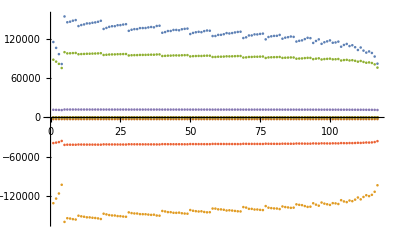

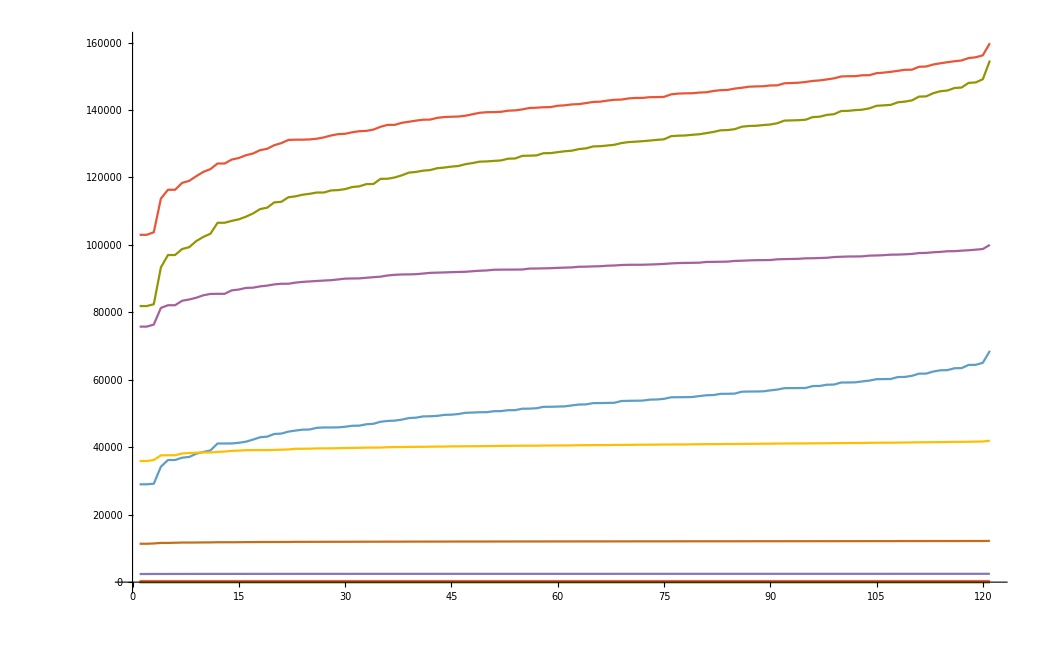

```mathematica
ListLinePlot[Sort[Table[Sort[Abs[Map[Coefficient[#,x,k]&,Select[Map[Last[FactorList[#]][[1]]&,Keys[byChromial]],Exponent[#,x]==9&]]]],{k,0,10}]]]
```

```mathematica
Table[Min[Abs[Map[Coefficient[#,x,k]&,Select[Map[Last[FactorList[#]][[1]]&,Keys[byChromial]],Exponent[#,x]==9&]]]],{k,0,10}]
```

{29012,81860,102981,75761,35913,11381,2415,332,27,1,0}

```mathematica
Table[Max[Abs[Map[Coefficient[#,x,k]&,Select[Map[Last[FactorList[#]][[1]]&,Keys[byChromial]],Exponent[#,x]==9&]]]],{k,0,10}]
```

{68578,154656,159801,100000,41933,12225,2472,333,27,1,0}

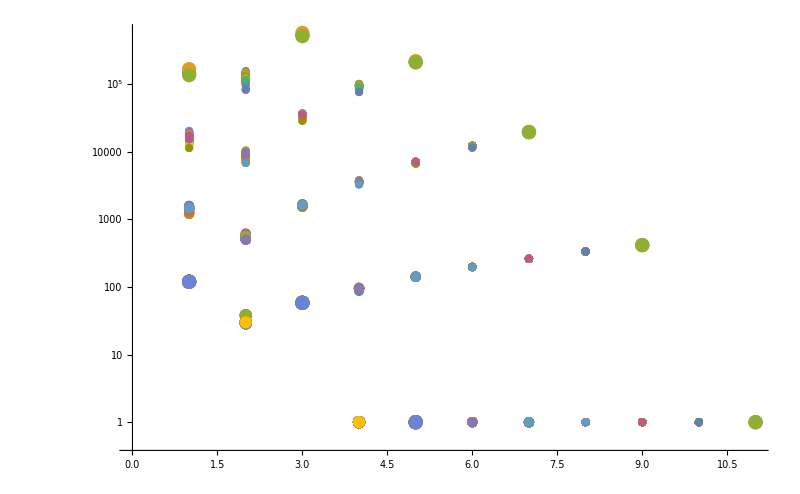

```mathematica
Show[Table[ListLogPlot[Map[CoefficientList[#,x]&,Select[  Map[Last[FactorList[#]][[1]]&,Keys[byChromial]] ,Exponent[#,x]==k&]], ImageSize->800],{k,10,3,-1}]]
```

```mathematica
Select[Keys[byChromial],Exponent[#,x]==9&]
```

{1458 x-5103 x^2+7533 x^3-6183 x^4+3105 x^5-981 x^6+191 x^7-21 x^8+x^9,1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9,1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9,2142 x-7035 x^2+9682 x^3-7406 x^4+3484 x^5-1042 x^6+195 x^7-21 x^8+x^9,1992 x-6640 x^2+9288 x^3-7217 x^4+3440 x^5-1038 x^6+195 x^7-21 x^8+x^9,2298 x-7465 x^2+10150 x^3-7670 x^4+3567 x^5-1056 x^6+196 x^7-21 x^8+x^9,2388 x-7696 x^2+10373 x^3-7773 x^4+3590 x^5-1058 x^6+196 x^7-21 x^8+x^9,2532 x-8062 x^2+10722 x^3-7932 x^4+3625 x^5-1061 x^6+196 x^7-21 x^8+x^9,2048 x-6784 x^2+9426 x^3-7279 x^4+3453 x^5-1039 x^6+195 x^7-21 x^8+x^9,2058 x-6839 x^2+9533 x^3-7378 x^4+3500 x^5-1050 x^6+196 x^7-21 x^8+x^9}

```mathematica
Length[byChromial]
```

502

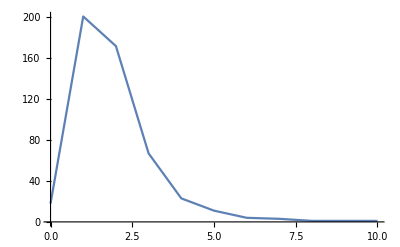

```mathematica
ListLinePlot[Sort[Tally[Map[ExpXMinus3[#]&,Keys[byChromial]]]]]
```

```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression,10000];Length[deps2]
```

10000

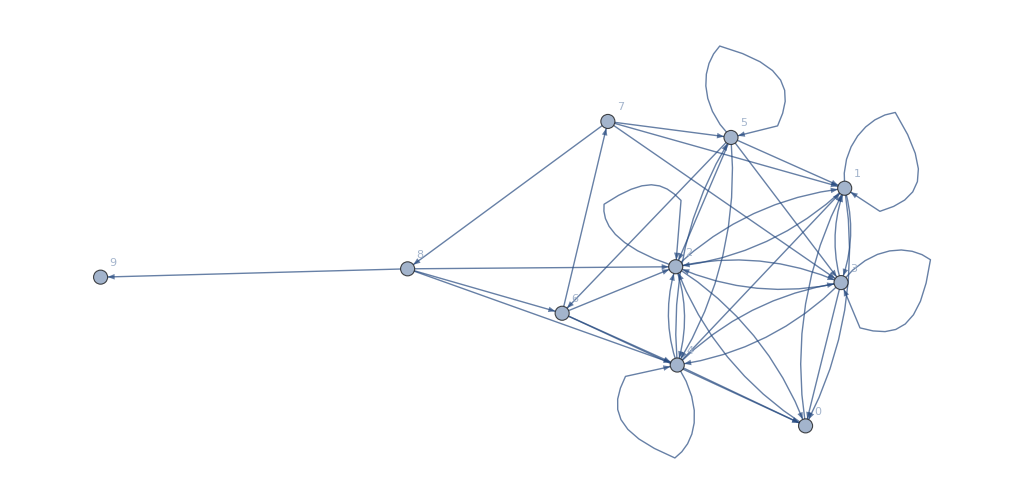

```mathematica
Graph[DeleteDuplicates[Map[ExpXMinus3[Chromial[#[[1]]]]->ExpXMinus3[Chromial[#[[2]]]]&,deps2]], VertexLabels->"Name"]
```

```mathematica
hhh=Map[CycleBaseCoeff[#]&, Map[Last[FactorList[#]][[1]]&,Keys[byChromial]]]
```

{{0,1},{0,1},{0,1},{-32,21,-6,1},{0,1},{-32,21,-6,1},{-35,22,-6,1},{0,1},{-35,22,-6,1},{-32,21,-6,1},{119,-86,28,-8,1},{-332,275,-101,44,-10,1},{0,1},{-32,21,-6,1},{-35,22,-6,1},{119,-86,28,-8,1},{-332,275,-101,44,-10,1},{-383,308,-110,45,-10,1},{-398,317,-112,45,-10,1},{-422,331,-115,45,-10,1},{-32,21,-6,1},{-49,29,-7,1},{0,1},{-35,22,-6,1},{-32,21,-6,1},{-332,275,-101,44,-10,1},{119,-86,28,-8,1},{-383,308,-110,45,-10,1},{-32,21,-6,1},{-398,317,-112,45,-10,1},{-422,331,-115,45,-10,1},{-35,22,-6,1},{-447,346,-119,46,-10,1},{-438,341,-118,46,-10,1},{1496,-1245,440,-216,66,-12,1},{-49,29,-7,1},{1199,-1038,376,-206,66,-12,1},{1271,-1090,393,-209,66,-12,1},{1385,-1170,418,-213,66,-12,1},{1454,-1217,432,-215,66,-12,1},{-3728,3381,-1169,800,-339,90,-14,1},{-3152,2905,-988,734,-330,90,-14,1},{0,1},{-32,21,-6,1},{-332,275,-101,44,-10,1},{-35,22,-6,1},{-383,308,-110,45,-10,1},{119,-86,28,-8,1},{1271,-1090,393,-209,66,-12,1},{-35,22,-6,1},{-398,317,-112,45,-10,1},{-35,22,-6,1},{-447,346,-119,46,-10,1},{1459,-1223,435,-219,67,-12,1},{1385,-1170,418,-213,66,-12,1},{-422,331,-115,45,-10,1},{1199,-1038,376,-206,66,-12,1},{-32,21,-6,1},{119,-86,28,-8,1},{1390,-1176,421,-217,67,-12,1},{-438,341,-118,46,-10,1},{-49,29,-7,1},{1454,-1217,432,-215,66,-12,1},{1569,-1296,456,-222,67,-12,1},{-3728,3381,-1169,800,-339,90,-14,1},{-5033,4410,-1537,926,-359,91,-14,1},{1501,-1251,443,-220,67,-12,1},{1496,-1245,440,-216,66,-12,1},{-4583,4066,-1417,891,-355,91,-14,1},{-332,275,-101,44,-10,1},{-4298,3843,-1337,866,-352,91,-14,1},{-4832,4257,-1484,910,-357,91,-14,1},{-5228,4555,-1586,938,-360,91,-14,1},{-4910,4317,-1505,917,-358,91,-14,1},{-4247,3802,-1322,860,-351,91,-14,1},{-3695,3360,-1159,808,-345,91,-14,1},{-3962,3577,-1240,837,-349,91,-14,1},{-3152,2905,-988,734,-330,90,-14,1},{-4382,3911,-1362,877,-354,91,-14,1},{-3907,3531,-1223,828,-347,91,-14,1},{-4712,4167,-1453,904,-357,91,-14,1},{-4508,4009,-1397,887,-355,91,-14,1},{-4043,3642,-1264,845,-350,91,-14,1},{13360,-12381,4007,-3136,1584,-535,119,-16,1},{-3195,2944,-1001,745,-335,91,-14,1},{-32,21,-6,1},{0,1},{-332,275,-101,44,-10,1},{-35,22,-6,1},{-383,308,-110,45,-10,1},{119,-86,28,-8,1},{1199,-1038,376,-206,66,-12,1},{-32,21,-6,1},{-35,22,-6,1},{1271,-1090,393,-209,66,-12,1},{1390,-1176,421,-217,67,-12,1},{119,-86,28,-8,1},{-398,317,-112,45,-10,1},{1385,-1170,418,-213,66,-12,1},{-438,341,-118,46,-10,1},{-447,346,-119,46,-10,1},{-3907,3531,-1223,828,-347,91,-14,1},{-49,29,-7,1},{-332,275,-101,44,-10,1},{-4298,3843,-1337,866,-352,91,-14,1},{-422,331,-115,45,-10,1},{-35,22,-6,1},{-3728,3381,-1169,800,-339,90,-14,1},{13559,-12564,4060,-3190,1615,-544,120,-16,1},{1459,-1223,435,-219,67,-12,1},{-383,308,-110,45,-10,1},{119,-86,28,-8,1},{1454,-1217,432,-215,66,-12,1},{1501,-1251,443,-220,67,-12,1},{-4247,3802,-1322,860,-351,91,-14,1},{-4925,4334,-1509,928,-364,92,-14,1},{1569,-1296,456,-222,67,-12,1},{-5033,4410,-1537,926,-359,91,-14,1},{-4910,4317,-1505,917,-358,91,-14,1},{1496,-1245,440,-216,66,-12,1},{-4603,4089,-1424,906,-362,92,-14,1},{-4043,3642,-1264,845,-350,91,-14,1},{-3962,3577,-1240,837,-349,91,-14,1},{-4508,4009,-1397,887,-355,91,-14,1},{-4382,3911,-1362,877,-354,91,-14,1},{-4712,4167,-1453,904,-357,91,-14,1},{-4852,4280,-1491,925,-364,92,-14,1},{-465,360,-124,47,-10,1},{16346,-14907,4929,-3586,1708,-553,120,-16,1},{-398,317,-112,45,-10,1},{-5053,4433,-1544,941,-366,92,-14,1},{-422,331,-115,45,-10,1},{-5048,4427,-1541,937,-365,92,-14,1},{-5248,4578,-1593,953,-367,92,-14,1},{-332,275,-101,44,-10,1},{-4847,4274,-1488,921,-363,92,-14,1},{-4832,4257,-1484,910,-357,91,-14,1},{14171,-13084,4255,-3280,1636,-546,120,-16,1},{-5127,4488,-1563,945,-366,92,-14,1},{-5370,4669,-1624,962,-368,92,-14,1},{-4583,4066,-1417,891,-355,91,-14,1},{-4803,4242,-1478,920,-363,92,-14,1},{13799,-12770,4137,-3229,1625,-545,120,-16,1},{15149,-13908,4562,-3419,1668,-549,120,-16,1},{18185,-16398,5473,-3793,1747,-556,120,-16,1},{-5228,4555,-1586,938,-360,91,-14,1},{17054,-15485,5142,-3668,1723,-554,120,-16,1},{-5562,4809,-1670,973,-369,92,-14,1},{15536,-14237,4682,-3483,1686,-551,120,-16,1},{-4318,3866,-1344,881,-359,92,-14,1},{-3695,3360,-1159,808,-345,91,-14,1},{-32,21,-6,1},{14404,-13281,4327,-3314,1645,-547,120,-16,1},{-5442,4721,-1641,965,-368,92,-14,1},{17279,-15670,5208,-3698,1731,-555,120,-16,1},{17621,-15944,5309,-3731,1735,-555,120,-16,1},{-3152,2905,-988,734,-330,90,-14,1},{16706,-15203,5037,-3631,1718,-554,120,-16,1},{16130,-14731,4863,-3563,1705,-553,120,-16,1},{13360,-12381,4007,-3136,1584,-535,119,-16,1},{14914,-13709,4488,-3383,1659,-548,120,-16,1},{-5172,4521,-1574,947,-366,92,-14,1},{-5635,4862,-1688,977,-369,92,-14,1},{17264,-15653,5204,-3687,1725,-554,120,-16,1},{16115,-14714,4859,-3552,1699,-552,120,-16,1},{16691,-15186,5033,-3620,1712,-553,120,-16,1},{15749,-14410,4747,-3503,1688,-551,120,-16,1},{18524,-16667,5571,-3825,1751,-556,120,-16,1},{-5488,4755,-1653,968,-368,92,-14,1},{17834,-16115,5372,-3753,1738,-555,120,-16,1},{14561,-13418,4378,-3345,1654,-548,120,-16,1},{14795,-13616,4451,-3380,1663,-549,120,-16,1},{-45860,43331,-12834,11477,-6778,2769,-789,152,-18,1},{-32,21,-6,1},{-4475,3989,-1389,894,-360,92,-14,1},{-5323,4634,-1613,958,-367,92,-14,1},{15386,-14109,4636,-3457,1678,-550,120,-16,1},{-4442,3962,-1379,889,-359,92,-14,1},{17966,-16221,5411,-3767,1740,-555,120,-16,1},{20170,-17964,6032,-3986,1779,-558,120,-16,1},{-41108,39075,-11282,10529,-6449,2707,-784,152,-18,1},{12179,-11382,3611,-2984,1569,-540,120,-16,1},{13589,-12598,4068,-3212,1627,-546,120,-16,1},{11279,-10594,3315,-2825,1525,-535,120,-16,1},{-36212,34639,-9671,9494,-6074,2634,-778,152,-18,1},{14810,-13633,4455,-3391,1669,-550,120,-16,1},{14201,-13118,4263,-3302,1648,-548,120,-16,1},{15764,-14427,4751,-3514,1694,-552,120,-16,1},{12575,-11726,3740,-3051,1587,-542,120,-16,1},{15179,-13942,4570,-3441,1680,-551,120,-16,1},{-3195,2944,-1001,745,-335,91,-14,1},{12311,-11492,3657,-2996,1567,-539,120,-16,1},{14314,-13205,4301,-3301,1640,-546,120,-16,1},{-29012,27999,-7339,7811,-5377,2477,-763,152,-18,1},{-383,308,-110,45,-10,1},{119,-86,28,-8,1},{-35,22,-6,1},{-32,21,-6,1},{-32,21,-6,1},{-35,22,-6,1},{-438,341,-118,46,-10,1},{-398,317,-112,45,-10,1},{1385,-1170,418,-213,66,-12,1},{119,-86,28,-8,1},{-447,346,-119,46,-10,1},{1199,-1038,376,-206,66,-12,1},{1390,-1176,421,-217,67,-12,1},{1271,-1090,393,-209,66,-12,1},{-332,275,-101,44,-10,1},{0,1},{-3907,3531,-1223,828,-347,91,-14,1},{-49,29,-7,1},{-332,275,-101,44,-10,1},{-3962,3577,-1240,837,-349,91,-14,1},{-4298,3843,-1337,866,-352,91,-14,1},{-422,331,-115,45,-10,1},{-35,22,-6,1},{-3728,3381,-1169,800,-339,90,-14,1},{13559,-12564,4060,-3190,1615,-544,120,-16,1},{1459,-1223,435,-219,67,-12,1},{-383,308,-110,45,-10,1},{1454,-1217,432,-215,66,-12,1},{1501,-1251,443,-220,67,-12,1},{-4247,3802,-1322,860,-351,91,-14,1},{-4603,4089,-1424,906,-362,92,-14,1},{-4382,3911,-1362,877,-354,91,-14,1},{-4043,3642,-1264,845,-350,91,-14,1},{119,-86,28,-8,1},{-4910,4317,-1505,917,-358,91,-14,1},{-4925,4334,-1509,928,-364,92,-14,1},{-5033,4410,-1537,926,-359,91,-14,1},{1569,-1296,456,-222,67,-12,1},{-4832,4257,-1484,910,-357,91,-14,1},{1496,-1245,440,-216,66,-12,1},{-42263,40146,-11600,10813,-6615,2767,-796,153,-18,1},{-3695,3360,-1159,808,-345,91,-14,1},{1199,-1038,376,-206,66,-12,1},{-4712,4167,-1453,904,-357,91,-14,1},{-4318,3866,-1344,881,-359,92,-14,1},{15581,-14286,4685,-3509,1709,-559,121,-16,1},{-5053,4433,-1544,941,-366,92,-14,1},{-32,21,-6,1},{-398,317,-112,45,-10,1},{-422,331,-115,45,-10,1},{-35,22,-6,1},{-44942,42547,-12474,11350,-6803,2803,-799,153,-18,1},{-447,346,-119,46,-10,1},{-398,317,-112,45,-10,1},{14404,-13281,4327,-3314,1645,-547,120,-16,1},{-438,341,-118,46,-10,1},{-4508,4009,-1397,887,-355,91,-14,1},{119,-86,28,-8,1},{-5048,4427,-1541,937,-365,92,-14,1},{-4852,4280,-1491,925,-364,92,-14,1},{-465,360,-124,47,-10,1},{1271,-1090,393,-209,66,-12,1},{16391,-14956,4932,-3612,1731,-561,121,-16,1},{-5248,4578,-1593,953,-367,92,-14,1},{17279,-15670,5208,-3698,1731,-555,120,-16,1},{-383,308,-110,45,-10,1},{-5127,4488,-1563,945,-366,92,-14,1},{-411,313,-106,41,-9,1},{15431,-14158,4639,-3483,1701,-558,121,-16,1},{-5370,4669,-1624,962,-368,92,-14,1},{17914,-16204,5386,-3805,1774,-565,121,-16,1},{16346,-14907,4929,-3586,1708,-553,120,-16,1},{-3728,3381,-1169,800,-339,90,-14,1},{1496,-1245,440,-216,66,-12,1},{-5655,4885,-1695,992,-376,93,-14,1},{-4847,4274,-1488,921,-363,92,-14,1},{-5442,4721,-1641,965,-368,92,-14,1},{14171,-13084,4255,-3280,1636,-546,120,-16,1},{16160,-14763,4862,-3578,1722,-560,121,-16,1},{15749,-14410,4747,-3503,1688,-551,120,-16,1},{-49178,46309,-13849,12160,-7075,2853,-803,153,-18,1},{-4583,4066,-1417,891,-355,91,-14,1},{1385,-1170,418,-213,66,-12,1},{-5228,4555,-1586,938,-360,91,-14,1},{17681,-16010,5316,-3768,1764,-564,121,-16,1},{18185,-16398,5473,-3793,1747,-556,120,-16,1},{17621,-15944,5309,-3731,1735,-555,120,-16,1},{-5562,4809,-1670,973,-369,92,-14,1},{13799,-12770,4137,-3229,1625,-545,120,-16,1},{14561,-13418,4378,-3345,1654,-548,120,-16,1},{-36212,34639,-9671,9494,-6074,2634,-778,152,-18,1},{-4442,3962,-1379,889,-359,92,-14,1},{12311,-11492,3657,-2996,1567,-539,120,-16,1},{15386,-14109,4636,-3457,1678,-550,120,-16,1},{-4475,3989,-1389,894,-360,92,-14,1},{-332,275,-101,44,-10,1},{-4803,4242,-1478,920,-363,92,-14,1},{-3152,2905,-988,734,-330,90,-14,1},{-32,21,-6,1},{15149,-13908,4562,-3419,1668,-549,120,-16,1},{16691,-15186,5033,-3620,1712,-553,120,-16,1},{-5172,4521,-1574,947,-366,92,-14,1},{-55832,52139,-15980,13354,-7458,2920,-808,153,-18,1},{18609,-16762,5588,-3881,1788,-566,121,-16,1},{17054,-15485,5142,-3668,1723,-554,120,-16,1},{16706,-15203,5037,-3631,1718,-554,120,-16,1},{15536,-14237,4682,-3483,1686,-551,120,-16,1},{17264,-15653,5204,-3687,1725,-554,120,-16,1},{16115,-14714,4859,-3552,1699,-552,120,-16,1},{-422,331,-115,45,-10,1},{15799,-14465,4753,-3533,1712,-559,121,-16,1},{16756,-15258,5043,-3661,1742,-562,121,-16,1},{-5820,5005,-1735,1003,-377,93,-14,1},{15566,-14269,4681,-3498,1703,-558,121,-16,1},{14226,-13145,4264,-3314,1661,-554,121,-16,1},{-45203,42780,-12561,11402,-6819,2805,-799,153,-18,1},{16165,-14769,4865,-3582,1723,-560,121,-16,1},{-51992,48785,-14758,12674,-7239,2881,-805,153,-18,1},{-47798,45081,-13410,11888,-6975,2832,-801,153,-18,1},{-44047,41739,-12194,11158,-6723,2784,-797,153,-18,1},{17899,-16187,5382,-3794,1768,-564,121,-16,1},{17686,-16016,5319,-3772,1765,-564,121,-16,1},{-57512,53593,-16513,13636,-7543,2934,-809,153,-18,1},{-5508,4778,-1660,983,-375,93,-14,1},{-41108,39075,-11282,10529,-6449,2707,-784,152,-18,1},{16130,-14731,4863,-3563,1705,-553,120,-16,1},{13360,-12381,4007,-3136,1584,-535,119,-16,1},{14914,-13709,4488,-3383,1659,-548,120,-16,1},{-50218,47217,-14192,12335,-7121,2858,-803,153,-18,1},{-5635,4862,-1688,977,-369,92,-14,1},{17324,-15719,5211,-3724,1754,-563,121,-16,1},{1454,-1217,432,-215,66,-12,1},{-332,275,-101,44,-10,1},{18604,-16756,5585,-3877,1787,-566,121,-16,1},{-53702,50279,-15308,12974,-7331,2896,-806,153,-18,1},{-60173,55876,-17356,14058,-7660,2951,-810,153,-18,1},{18250,-16470,5483,-3834,1777,-565,121,-16,1},{18816,-16925,5647,-3899,1790,-566,121,-16,1},{-55403,51760,-15851,13269,-7422,2911,-807,153,-18,1},{-5847,5024,-1741,1004,-377,93,-14,1},{-5488,4755,-1653,968,-368,92,-14,1},{18255,-16476,5486,-3838,1778,-565,121,-16,1},{17834,-16115,5372,-3753,1738,-555,120,-16,1},{19374,-17369,5805,-3959,1802,-567,121,-16,1},{18524,-16667,5571,-3825,1751,-556,120,-16,1},{19500,-17467,5840,-3969,1803,-567,121,-16,1},{-63452,58675,-18373,14573,-7813,2977,-812,153,-18,1},{19711,-17634,5901,-3991,1806,-567,121,-16,1},{-61817,57282,-17868,14318,-7737,2964,-811,153,-18,1},{15229,-13997,4576,-3471,1704,-559,121,-16,1},{14626,-13490,4388,-3386,1684,-557,121,-16,1},{14251,-13173,4269,-3332,1672,-556,121,-16,1},{16411,-14979,4939,-3627,1738,-562,121,-16,1},{15829,-14499,4761,-3555,1724,-561,121,-16,1},{15946,-14589,4796,-3557,1720,-560,121,-16,1},{16771,-15275,5047,-3672,1748,-563,121,-16,1},{17134,-15574,5156,-3720,1759,-564,121,-16,1},{15451,-14181,4646,-3498,1708,-559,121,-16,1},{-55907,52222,-15991,13402,-7493,2930,-809,153,-18,1},{17349,-15748,5221,-3743,1762,-564,121,-16,1},{18481,-16661,5551,-3870,1787,-566,121,-16,1},{-59243,55100,-17046,13950,-7656,2957,-811,153,-18,1},{-53138,49807,-15110,12915,-7338,2903,-807,153,-18,1},{16761,-15264,5046,-3665,1743,-562,121,-16,1},{-57527,53610,-16517,13647,-7549,2935,-809,153,-18,1},{-59198,55051,-17043,13924,-7633,2949,-810,153,-18,1},{17119,-15557,5152,-3709,1753,-563,121,-16,1},{14201,-13118,4263,-3302,1648,-548,120,-16,1},{12575,-11726,3740,-3051,1587,-542,120,-16,1},{15179,-13942,4570,-3441,1680,-551,120,-16,1},{-51437,48322,-14560,12622,-7251,2889,-806,153,-18,1},{14810,-13633,4455,-3391,1669,-550,120,-16,1},{15764,-14427,4751,-3514,1694,-552,120,-16,1},{-5323,4634,-1613,958,-367,92,-14,1},{13589,-12598,4068,-3212,1627,-546,120,-16,1},{12179,-11382,3611,-2984,1569,-540,120,-16,1},{14795,-13616,4451,-3380,1663,-549,120,-16,1},{-54845,51296,-15657,13214,-7430,2918,-808,153,-18,1},{-53822,50411,-15322,13048,-7389,2914,-808,153,-18,1},{-54830,51279,-15653,13203,-7424,2917,-808,153,-18,1},{-57572,53659,-16520,13673,-7572,2943,-810,153,-18,1},{16185,-14792,4872,-3597,1730,-561,121,-16,1},{-56528,52755,-16193,13497,-7515,2932,-809,153,-18,1},{-52112,48917,-14772,12748,-7297,2899,-807,153,-18,1},{142984,-137591,35671,-37107,25825,-12642,4435,-1107,189,-20,1},{-55172,51563,-15774,13237,-7417,2911,-807,153,-18,1},{16609,-15134,4998,-3637,1735,-561,121,-16,1},{-60233,55942,-17363,14095,-7689,2960,-811,153,-18,1},{14479,-13365,4343,-3363,1677,-556,121,-16,1},{14314,-13205,4301,-3301,1640,-546,120,-16,1},{-46070,43557,-12839,11580,-6885,2818,-800,153,-18,1},{-50990,47921,-14424,12525,-7209,2879,-805,153,-18,1},{-54800,51247,-15654,13188,-7407,2910,-807,153,-18,1},{-52400,49143,-14890,12749,-7262,2884,-805,153,-18,1},{-58142,54135,-16715,13738,-7570,2937,-809,153,-18,1},{17691,-16022,5322,-3776,1766,-564,121,-16,1},{16401,-14968,4938,-3620,1733,-561,121,-16,1},{-54158,50689,-15444,13078,-7378,2907,-807,153,-18,1},{17329,-15725,5214,-3728,1755,-563,121,-16,1},{-46955,44332,-13138,11726,-6919,2821,-800,153,-18,1},{-49652,46741,-13992,12276,-7128,2865,-804,153,-18,1},{-58580,54523,-16844,13830,-7611,2947,-810,153,-18,1},{-56858,53025,-16311,13523,-7503,2925,-808,153,-18,1},{-57542,53627,-16521,13658,-7555,2936,-809,153,-18,1},{-56468,52689,-16186,13460,-7486,2923,-808,153,-18,1},{-62813,58128,-18182,14469,-7775,2968,-811,153,-18,1},{-60800,56413,-17555,14159,-7687,2954,-810,153,-18,1},{-62438,57811,-18063,14415,-7763,2967,-811,153,-18,1},{-61832,57299,-17872,14329,-7743,2965,-811,153,-18,1},{-60845,56462,-17558,14185,-7710,2962,-811,153,-18,1},{18946,-17028,5684,-3912,1792,-566,121,-16,1},{18046,-16310,5425,-3819,1776,-565,121,-16,1},{18031,-16293,5421,-3808,1770,-564,121,-16,1},{18265,-16487,5487,-3845,1783,-566,121,-16,1},{-62858,58177,-18185,14495,-7798,2976,-812,153,-18,1},{-55478,51843,-15862,13317,-7457,2921,-808,153,-18,1},{-53792,50379,-15323,13033,-7372,2907,-807,153,-18,1},{-49592,46675,-13985,12239,-7099,2856,-803,153,-18,1},{19164,-17203,5745,-3938,1799,-567,121,-16,1},{18466,-16644,5547,-3859,1781,-565,121,-16,1},{19716,-17639,5899,-3994,1810,-568,121,-16,1},{-49847,46900,-14068,12287,-7114,2858,-803,153,-18,1},{-53093,49758,-15107,12889,-7315,2895,-806,153,-18,1},{-35,22,-6,1},{14835,-13660,4456,-3403,1682,-556,121,-16,1},{-332,275,-101,44,-10,1},{14989,-13793,4504,-3432,1691,-557,121,-16,1},{-43142,40939,-11886,10999,-6683,2780,-797,153,-18,1},{-48182,45449,-13512,12017,-7050,2852,-803,153,-18,1},{-49138,46265,-13844,12137,-7056,2846,-802,153,-18,1},{17966,-16221,5411,-3767,1740,-555,120,-16,1},{-50678,47633,-14332,12441,-7168,2869,-804,153,-18,1},{16019,-14646,4821,-3559,1716,-559,121,-16,1},{-53078,49741,-15103,12878,-7309,2894,-806,153,-18,1},{-59183,55034,-17039,13913,-7627,2948,-810,153,-18,1},{-50288,47295,-14205,12380,-7152,2867,-804,153,-18,1},{-63422,58643,-18374,14558,-7796,2970,-811,153,-18,1},{18821,-16931,5650,-3903,1791,-566,121,-16,1},{17696,-16028,5325,-3780,1767,-564,121,-16,1},{19505,-17473,5843,-3973,1804,-567,121,-16,1},{-65033,60006,-18868,14797,-7865,2982,-812,153,-18,1},{-45860,43331,-12834,11477,-6778,2769,-789,152,-18,1},{-58535,54474,-16841,13804,-7588,2939,-809,153,-18,1},{-64430,59499,-18680,14712,-7845,2980,-812,153,-18,1},{-46358,43819,-12927,11646,-6915,2826,-801,153,-18,1},{15809,-14477,4759,-3541,1714,-559,121,-16,1},{-52658,49371,-14974,12800,-7278,2886,-805,153,-18,1},{-54113,50640,-15441,13052,-7355,2899,-806,153,-18,1},{-68578,62982,-19956,15305,-7997,3000,-813,153,-18,1},{20170,-17964,6032,-3986,1779,-558,120,-16,1},{-58172,54169,-16723,13760,-7582,2939,-809,153,-18,1},{13246,-12314,3948,-3176,1633,-552,121,-16,1},{15076,-13865,4527,-3443,1696,-558,121,-16,1},{11279,-10594,3315,-2825,1525,-535,120,-16,1},{-51982,48773,-14752,12666,-7237,2881,-805,153,-18,1},{-56513,52738,-16189,13486,-7509,2931,-809,153,-18,1},{-56573,52804,-16196,13523,-7538,2940,-810,153,-18,1},{-54890,51345,-15660,13240,-7453,2926,-809,153,-18,1},{19159,-17198,5747,-3935,1795,-566,121,-16,1},{-52703,49420,-14977,12826,-7301,2894,-806,153,-18,1},{-60203,55910,-17364,14080,-7672,2953,-810,153,-18,1},{-54347,50840,-15516,13085,-7363,2900,-806,153,-18,1},{-61172,56727,-17673,14210,-7698,2955,-810,153,-18,1},{-55847,52156,-15984,13365,-7464,2921,-808,153,-18,1},{-53762,50345,-15315,13011,-7360,2905,-807,153,-18,1},{-59522,55313,-17157,13946,-7620,2942,-809,153,-18,1},{-3195,2944,-1001,745,-335,91,-14,1},{-53183,49856,-15113,12941,-7361,2911,-808,153,-18,1},{-57095,53228,-16387,13559,-7512,2926,-808,153,-18,1},{-59762,55519,-17234,13985,-7630,2943,-809,153,-18,1},{-50393,47410,-14215,12443,-7204,2884,-806,153,-18,1},{-51422,48305,-14556,12611,-7245,2888,-806,153,-18,1},{-51563,48404,-14624,12589,-7206,2873,-804,153,-18,1},{18599,-16751,5587,-3874,1783,-565,121,-16,1},{17909,-16199,5388,-3802,1770,-564,121,-16,1},{-64400,59467,-18681,14697,-7828,2973,-811,153,-18,1},{164944,-157759,42651,-42100,27969,-13196,4515,-1112,189,-20,1},{-52052,48851,-14765,12711,-7268,2890,-806,153,-18,1},{-50975,47904,-14420,12514,-7203,2878,-805,153,-18,1},{-46808,44225,-13066,11744,-6957,2836,-802,153,-18,1},{-45263,42846,-12568,11439,-6848,2814,-800,153,-18,1},{-48763,45943,-13718,12086,-7048,2846,-802,153,-18,1},{-46403,43868,-12930,11672,-6938,2834,-802,153,-18,1},{-50708,47667,-14340,12463,-7180,2871,-804,153,-18,1},{-3152,2905,-988,734,-330,90,-14,1},{-41318,39301,-11287,10632,-6556,2756,-795,153,-18,1},{-47888,45181,-13425,11947,-7016,2843,-802,153,-18,1},{17475,-15848,5261,-3753,1760,-563,121,-16,1},{-41123,39120,-11231,10582,-6529,2748,-794,153,-18,1},{-42955,40767,-11831,10954,-6660,2773,-796,153,-18,1},{-41642,39603,-11378,10717,-6604,2771,-797,153,-18,1},{-37118,35493,-9910,9734,-6226,2692,-790,153,-18,1},{-45752,43295,-12711,11559,-6909,2831,-802,153,-18,1},{-43928,41661,-12119,11190,-6778,2806,-800,153,-18,1},{-38603,36850,-10386,10068,-6363,2723,-793,153,-18,1},{-47552,44899,-13292,11912,-7033,2855,-804,153,-18,1},{-49298,46441,-13863,12234,-7133,2871,-805,153,-18,1},{-34223,32836,-8978,9070,-5952,2630,-784,153,-18,1},{-36903,35290,-9853,9675,-6189,2679,-788,153,-18,1},{-38083,36365,-10238,9933,-6288,2700,-790,153,-18,1},{-50378,47393,-14211,12432,-7198,2883,-806,153,-18,1},{-44630,42291,-12345,11333,-6831,2817,-801,153,-18,1},{134344,-129591,32947,-35073,24906,-12387,4394,-1104,189,-20,1},{-39062,37269,-10532,10171,-6406,2733,-794,153,-18,1},{-48650,45873,-13647,12122,-7104,2868,-805,153,-18,1},{-29012,27999,-7339,7811,-5377,2477,-763,152,-18,1},{-45887,43390,-12786,11538,-6863,2811,-799,153,-18,1},{-29183,28165,-7373,7857,-5417,2499,-770,153,-18,1}}

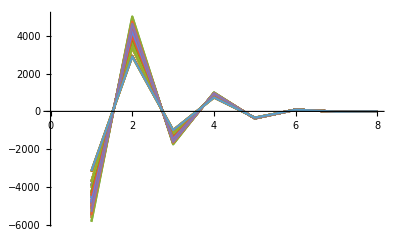

```mathematica
ListLinePlot[Select[hhh,Length[#]==8&]]
```

```mathematica
down=Select[deps2,Chrom[#[[1]]]>Chrom[#[[2]]]&]
```

{{6,18,{2,3<->5,1<->4}},{7,18,{2,1<->5,2<->7}},{11,38,{2,3<->6,2<->4}},{11,36,{2,3<->4,6<->8}},{14,38,{2,3<->5,4<->7}},{15,38,{2,3<->5,4<->7}},{15,36,{2,5<->6,4<->8}},{18,46,{2,2<->5,6<->7}},{19,36,{2,5<->6,2<->4}},{20,38,{2,3<->6,2<->4}},{21,40,{2,1<->5,2<->7}},{25,94,{2,2<->5,6<->7}},{25,88,{2,5<->6,2<->4}},{25,99,{2,6<->8,4<->9}},{26,88,{2,2<->6,3<->9}},{26,113,{2,5<->8,3<->4}},{26,99,{2,4<->5,8<->9}},{30,88,{2,2<->5,6<->9}},{31,94,{2,3<->6,2<->8}},{31,159,{2,5<->7,2<->9}},{31,172,{2,3<->9,7<->8}},{35,159,{2,2<->5,7<->9}},{35,123,{2,6<->8,3<->4}},{35,99,{2,8<->9,4<->5}},{36,108,{2,3<->6,2<->8}},{36,122,{2,5<->9,4<->7}},{37,91,{2,3<->4,6<->8}},{37,205,{2,2<->7,1<->5}},{37,206,{2,2<->5,7<->9}},{37,207,{2,3<->7,1<->8}},{37,208,{2,3<->8,4<->7}},{38,216,{2,2<->5,6<->7}},{38,108,{2,4<->5,6<->8}},{38,122,{2,3<->4,8<->9}},{39,217,{2,3<->6,2<->4}},{39,123,{2,3<->4,6<->8}},{39,113,{2,2<->5,6<->7}},{39,88,{2,3<->8,4<->7}},{40,215,{2,2<->5,6<->9}},{40,207,{2,1<->7,3<->9}},{41,215,{2,2<->5,6<->7}},{42,187,{2,3<->4,6<->8}},{42,221,{2,2<->5,6<->7}},{42,223,{2,5<->6,2<->4}},{43,220,{2,2<->5,6<->7}},{43,196,{2,4<->5,6<->8}},{43,222,{2,3<->8,4<->7}},{44,220,{2,3<->6,2<->4}},{44,188,{2,3<->4,6<->8}},{45,221,{2,3<->6,2<->4}},{45,197,{2,3<->4,6<->8}},{49,123,{2,2<->7,1<->9}},{49,113,{2,3<->7,1<->5}},{49,220,{2,3<->5,7<->8}},{49,196,{2,5<->6,8<->9}},{56,217,{2,2<->5,8<->9}},{57,113,{2,3<->6,4<->9}},{57,88,{2,5<->6,4<->8}},{57,220,{2,2<->5,7<->8}},{62,218,{2,3<->5,4<->7}},{63,221,{2,3<->5,4<->7}},{64,223,{2,3<->5,4<->7}},{64,217,{2,2<->8,6<->9}},{65,221,{2,3<->5,4<->7}},{65,187,{2,5<->6,4<->8}},{65,222,{2,2<->6,8<->9}},{66,188,{2,3<->5,4<->7}},{66,222,{2,2<->6,3<->9}},{67,172,{2,3<->5,4<->7}},{67,197,{2,2<->7,1<->8}},{67,187,{2,3<->7,1<->5}},{67,188,{2,6<->8,2<->9}},{72,205,{2,1<->5,2<->7}},{76,386,{2,5<->8,3<->4}},{76,346,{2,4<->5,8<->10}},{76,387,{2,3<->6,8<->9}},{76,389,{2,6<->9,3<->10}},{76,391,{2,5<->10,4<->9}},{78,389,{2,2<->5,9<->10}},{79,346,{2,2<->7,1<->10}},{79,389,{2,3<->7,1<->5}},{79,463,{2,3<->9,2<->6}},{79,381,{2,5<->9,6<->10}},{80,378,{2,5<->6,4<->9}},{80,442,{2,2<->7,1<->5}},{80,437,{2,2<->5,7<->9}},{80,485,{2,3<->9,2<->6}},{82,463,{2,2<->5,7<->9}},{88,591,{2,3<->6,8<->9}},{88,593,{2,5<->10,2<->4}},{88,413,{2,6<->10,4<->9}},{89,510,{2,3<->9,2<->6}},{89,601,{2,5<->10,6<->7}},{89,381,{2,6<->10,5<->9}},{89,483,{2,2<->10,7<->9}},{89,463,{2,7<->10,2<->5}},{90,477,{2,3<->6,8<->9}},{90,600,{2,3<->8,6<->10}},{90,511,{2,3<->9,2<->6}},{90,585,{2,2<->5,9<->10}},{90,620,{2,5<->10,2<->8}},{91,457,{2,2<->7,1<->5}},{91,408,{2,2<->5,7<->9}},{91,629,{2,3<->10,1<->8}},{91,489,{2,5<->10,7<->8}},{91,378,{2,1<->10,3<->7}},{93,410,{2,6<->8,3<->4}},{93,347,{2,3<->9,2<->6}},{93,585,{2,5<->9,2<->10}},{93,411,{2,6<->10,4<->9}},{93,346,{2,8<->10,4<->5}},{94,658,{2,3<->5,7<->8}},{94,617,{2,2<->6,9<->10}},{95,600,{2,2<->5,6<->7}},{96,657,{2,2<->5,6<->7}},{96,601,{2,5<->6,2<->10}},{96,620,{2,3<->5,7<->8}},{96,483,{2,6<->8,9<->10}},{97,620,{2,2<->5,6<->7}},{97,431,{2,5<->6,2<->4}},{97,698,{2,6<->8,4<->9}},{98,588,{2,2<->5,6<->10}},{98,456,{2,5<->6,2<->4}},{98,708,{2,6<->8,4<->9}},{99,413,{2,5<->6,2<->4}},{99,591,{2,6<->9,2<->10}},{100,463,{2,2<->6,5<->10}},{100,601,{2,3<->8,5<->9}},{100,725,{2,3<->9,8<->10}},{100,727,{2,3<->10,2<->9}},{101,661,{2,3<->5,7<->8}},{101,597,{2,5<->8,3<->4}},{101,718,{2,6<->8,4<->9}},{101,510,{2,2<->6,9<->10}},{102,600,{2,2<->5,6<->7}},{102,594,{2,5<->6,2<->4}},{102,657,{2,3<->5,7<->8}},{102,391,{2,5<->8,3<->4}},{102,411,{2,6<->8,4<->9}},{103,538,{2,5<->6,2<->4}},{103,661,{2,3<->5,7<->8}},{103,523,{2,5<->8,3<->4}},{103,719,{2,6<->8,4<->9}},{104,662,{2,2<->5,6<->7}},{104,550,{2,5<->6,2<->4}},{104,720,{2,6<->8,4<->9}},{104,727,{2,2<->9,6<->10}},{105,663,{2,2<->5,6<->7}},{105,510,{2,2<->6,5<->10}},{105,564,{2,5<->6,2<->4}},{105,664,{2,3<->5,7<->8}},{105,598,{2,5<->8,3<->4}},{105,721,{2,6<->8,4<->9}},{105,727,{2,2<->9,3<->10}},{105,725,{2,6<->9,8<->10}},{106,665,{2,2<->5,6<->7}},{106,599,{2,5<->6,2<->4}},{106,725,{2,6<->9,2<->10}},{107,793,{2,2<->6,9<->10}},{107,629,{2,2<->10,1<->6}},{107,489,{2,5<->10,6<->7}},{109,627,{2,3<->5,7<->8}},{109,667,{2,3<->9,2<->8}},{109,617,{2,9<->10,2<->6}},{110,431,{2,2<->6,3<->9}},{110,805,{2,5<->8,3<->4}},{110,698,{2,4<->5,8<->9}},{111,456,{2,2<->6,3<->9}},{111,602,{2,3<->5,7<->8}},{111,708,{2,4<->5,8<->9}},{112,388,{2,2<->6,3<->9}},{112,792,{2,2<->5,7<->9}},{112,337,{2,4<->5,8<->9}},{112,824,{2,5<->9,2<->4}},{113,593,{2,3<->6,2<->8}},{113,413,{2,4<->6,8<->9}},{113,591,{2,4<->5,9<->10}},{114,834,{2,5<->8,3<->4}},{114,720,{2,4<->5,8<->9}},{115,391,{2,2<->6,3<->9}},{115,594,{2,3<->6,2<->8}},{115,387,{2,5<->8,3<->4}},{115,411,{2,4<->5,8<->9}},{115,835,{2,5<->9,2<->4}},{116,523,{2,2<->6,3<->9}},{116,538,{2,3<->6,2<->8}},{116,719,{2,4<->5,8<->9}},{116,836,{2,5<->9,2<->4}},{117,595,{2,2<->6,3<->9}},{117,597,{2,3<->6,2<->8}},{117,718,{2,4<->5,8<->9}},{117,841,{2,6<->8,3<->4}},{117,838,{2,5<->9,2<->4}},{118,596,{2,2<->6,3<->9}},{118,837,{2,5<->8,3<->4}},{118,721,{2,4<->5,8<->9}},{118,839,{2,5<->9,2<->4}},{119,347,{2,2<->6,3<->9}},{119,600,{2,3<->6,2<->8}},{119,657,{2,5<->8,3<->4}},{119,722,{2,4<->5,8<->9}},{119,840,{2,5<->9,2<->4}},{120,602,{2,2<->6,3<->9}},{120,605,{2,3<->6,2<->8}},{120,636,{2,3<->5,7<->8}},{121,606,{2,3<->6,2<->8}},{121,792,{2,2<->10,6<->7}},{121,793,{2,6<->10,2<->9}},{123,604,{2,2<->6,3<->9}},{123,591,{2,5<->8,4<->10}},{123,814,{2,6<->8,3<->4}},{123,413,{2,2<->5,9<->10}},{125,391,{2,2<->5,6<->10}},{134,722,{2,2<->5,7<->10}},{134,895,{2,3<->5,7<->8}},{136,594,{2,2<->5,6<->10}},{145,477,{2,5<->6,2<->9}},{146,606,{2,3<->6,2<->8}},{146,408,{2,6<->8,3<->9}},{147,601,{2,2<->5,6<->10}},{147,391,{2,2<->9,1<->10}},{147,387,{2,3<->9,1<->7}},{149,620,{2,3<->6,2<->8}},{149,657,{2,2<->5,6<->7}},{149,1084,{2,5<->7,2<->10}},{149,895,{2,3<->8,6<->10}},{149,599,{2,3<->10,7<->8}},{151,431,{2,3<->6,2<->8}},{151,805,{2,5<->6,2<->4}},{158,1084,{2,2<->5,7<->10}},{158,815,{2,6<->8,3<->4}},{158,698,{2,8<->10,4<->5}},{159,667,{2,2<->5,6<->7}},{159,904,{2,3<->10,8<->9}},{159,789,{2,5<->10,7<->8}},{160,594,{2,1<->9,2<->7}},{160,410,{2,1<->7,9<->10}},{160,389,{2,1<->10,3<->7}},{161,456,{2,3<->6,2<->8}},{161,458,{2,3<->5,7<->10}},{162,597,{2,2<->5,6<->9}},{164,595,{2,2<->5,6<->9}},{164,389,{2,3<->7,1<->10}},{164,386,{2,5<->7,9<->10}},{165,538,{2,2<->5,6<->9}},{166,523,{2,2<->5,6<->9}},{167,594,{2,2<->9,1<->10}},{167,835,{2,5<->9,7<->10}},{168,596,{2,2<->5,6<->9}},{168,386,{2,5<->7,3<->10}},{168,410,{2,7<->9,1<->10}},{168,835,{2,5<->9,2<->10}},{169,634,{2,3<->5,7<->8}},{169,708,{2,6<->8,3<->4}},{170,844,{2,3<->10,1<->8}},{170,408,{2,1<->10,3<->7}},{171,458,{2,2<->6,3<->5}},{171,605,{2,3<->6,2<->8}},{171,405,{2,4<->6,5<->8}},{172,904,{2,5<->7,2<->9}},{173,659,{2,3<->6,2<->8}},{173,738,{2,5<->6,2<->4}},{173,500,{2,2<->7,1<->5}},{173,633,{2,5<->7,2<->10}},{173,378,{2,3<->7,1<->10}},{173,553,{2,3<->9,8<->10}},{174,661,{2,2<->5,6<->7}},{174,1112,{2,5<->7,2<->9}},{174,1121,{2,3<->8,6<->9}},{174,1189,{2,3<->9,7<->8}},{175,661,{2,3<->6,2<->8}},{175,1139,{2,3<->8,6<->9}},{175,1190,{2,3<->9,7<->8}},{176,665,{2,3<->6,2<->8}},{176,662,{2,2<->5,6<->7}},{176,1140,{2,5<->7,2<->9}},{177,664,{2,3<->6,2<->8}},{177,663,{2,2<->5,6<->7}},{177,1142,{2,3<->8,6<->9}},{177,1191,{2,3<->9,7<->8}},{186,1112,{2,2<->5,7<->10}},{186,511,{2,3<->6,8<->9}},{186,856,{2,6<->8,3<->4}},{186,720,{2,8<->10,4<->5}},{187,770,{2,3<->5,7<->8}},{187,855,{2,6<->10,2<->4}},{188,754,{2,2<->5,6<->7}},{188,905,{2,3<->10,1<->8}},{188,800,{2,5<->10,7<->8}},{189,511,{2,2<->6,5<->9}},{189,890,{2,2<->7,1<->5}},{189,721,{2,3<->7,1<->10}},{189,840,{2,3<->6,9<->10}},{189,1121,{2,6<->10,3<->8}},{189,1139,{2,5<->10,7<->8}},{195,1140,{2,3<->5,7<->8}},{195,719,{2,6<->8,3<->4}},{195,873,{2,6<->10,2<->4}},{196,783,{2,3<->10,1<->8}},{196,754,{2,5<->10,7<->8}},{197,770,{2,3<->6,2<->8}},{201,1142,{2,2<->5,7<->9}},{201,840,{2,3<->8,6<->10}},{201,906,{2,6<->8,3<->4}},{201,718,{2,8<->9,4<->5}},{201,599,{2,5<->8,9<->10}},{201,883,{2,6<->9,2<->4}},{202,636,{2,2<->6,3<->9}},{203,1292,{2,2<->5,7<->9}},{203,1293,{2,3<->7,1<->8}},{203,500,{2,3<->4,8<->10}},{203,1294,{2,3<->8,4<->7}},{203,442,{2,3<->10,4<->6}},{204,436,{2,3<->4,6<->8}},{204,375,{2,3<->6,4<->9}},{204,832,{2,2<->5,7<->9}},{204,1292,{2,2<->7,5<->10}},{204,1304,{2,5<->7,2<->8}},{204,592,{2,3<->8,4<->7}},{204,1301,{2,3<->7,8<->10}},{204,1305,{2,3<->9,2<->6}},{205,458,{2,3<->4,6<->8}},{205,1302,{2,3<->7,1<->8}},{205,1316,{2,3<->8,4<->7}},{206,1319,{2,3<->7,1<->8}},{206,844,{2,5<->7,8<->10}},{206,1301,{2,2<->9,3<->10}},{206,1321,{2,3<->9,2<->6}},{206,739,{2,5<->9,6<->10}},{206,1323,{2,7<->10,2<->5}},{207,1302,{2,2<->7,1<->5}},{207,1318,{2,3<->8,4<->10}},{208,629,{2,3<->4,6<->10}},{208,489,{2,4<->5,6<->8}},{208,1321,{2,5<->7,2<->8}},{208,1319,{2,3<->7,1<->10}},{208,738,{2,4<->8,5<->10}},{208,1303,{2,4<->10,3<->8}},{209,524,{2,4<->5,6<->8}},{209,442,{2,4<->6,5<->10}},{209,457,{2,3<->7,1<->8}},{209,1332,{2,3<->8,4<->7}},{210,526,{2,3<->4,6<->8}},{210,1323,{2,3<->7,1<->8}},{210,1333,{2,3<->8,4<->7}},{211,457,{2,3<->4,6<->10}},{211,570,{2,3<->6,4<->9}},{211,632,{2,4<->5,6<->8}},{211,500,{2,2<->7,1<->5}},{211,1327,{2,5<->7,2<->8}},{211,1303,{2,3<->7,1<->8}},{212,631,{2,3<->4,6<->8}},{212,556,{2,3<->6,4<->9}},{212,1294,{2,2<->7,1<->5}},{212,1324,{2,2<->5,7<->9}},{212,1326,{2,5<->7,2<->8}},{212,1303,{2,3<->8,4<->10}},{213,630,{2,3<->4,6<->8}},{213,567,{2,3<->6,4<->9}},{213,1294,{2,2<->7,1<->5}},{213,1325,{2,2<->5,7<->9}},{213,1323,{2,5<->7,2<->10}},{213,738,{2,5<->8,4<->10}},{214,1321,{2,5<->7,2<->10}},{214,1318,{2,3<->7,1<->8}},{214,739,{2,5<->6,9<->10}},{214,629,{2,7<->10,5<->8}},{214,489,{2,6<->10,4<->5}},{215,1318,{2,2<->7,1<->5}},{217,593,{2,2<->5,6<->7}},{217,604,{2,4<->5,6<->8}},{217,814,{2,3<->4,8<->9}},{218,1330,{2,2<->5,6<->10}},{218,602,{2,2<->6,5<->9}},{218,605,{2,4<->5,6<->8}},{218,1316,{2,4<->8,3<->5}},{219,1321,{2,2<->5,6<->7}},{220,754,{2,4<->5,6<->8}},{220,783,{2,3<->4,8<->9}},{221,770,{2,4<->5,6<->8}},{222,754,{2,2<->5,6<->7}},{223,855,{2,2<->5,6<->7}},{223,776,{2,4<->5,6<->8}},{224,1318,{2,1<->7,3<->10}},{225,1343,{2,3<->6,2<->4}},{225,815,{2,3<->4,6<->8}},{225,805,{2,2<->5,6<->7}},{225,431,{2,3<->8,4<->7}},{226,856,{2,3<->4,6<->8}},{226,834,{2,2<->5,6<->7}},{226,1347,{2,5<->6,2<->4}},{226,550,{2,3<->8,4<->7}},{227,837,{2,2<->5,6<->7}},{227,1348,{2,5<->6,2<->4}},{227,891,{2,4<->5,6<->8}},{227,1273,{2,5<->7,2<->8}},{227,564,{2,3<->8,4<->7}},{228,1344,{2,3<->6,2<->4}},{228,890,{2,3<->4,6<->8}},{228,1348,{2,5<->7,2<->8}},{228,598,{2,3<->8,4<->7}},{229,1345,{2,3<->6,2<->4}},{229,883,{2,3<->4,6<->8}},{229,597,{2,3<->8,4<->7}},{230,1346,{2,3<->6,2<->4}},{230,842,{2,2<->5,6<->7}},{230,882,{2,4<->5,6<->8}},{230,1344,{2,5<->7,2<->8}},{230,596,{2,5<->8,4<->7}},{231,1223,{2,3<->6,2<->4}},{231,906,{2,3<->4,6<->8}},{231,841,{2,2<->5,6<->7}},{231,1345,{2,5<->7,2<->8}},{231,595,{2,5<->8,4<->7}},{232,538,{2,3<->6,2<->4}},{232,873,{2,3<->4,6<->8}},{232,836,{2,2<->5,6<->7}},{233,791,{2,2<->5,6<->9}},{234,1351,{2,2<->5,6<->7}},{234,1259,{2,4<->5,6<->8}},{234,1251,{2,3<->8,4<->7}},{235,1237,{2,3<->4,6<->8}},{235,1351,{2,5<->7,2<->8}},{235,1246,{2,3<->8,4<->7}},{236,1281,{2,2<->5,6<->7}},{236,1352,{2,5<->6,2<->4}},{236,1256,{2,4<->5,6<->8}},{237,1244,{2,4<->5,6<->8}},{237,1260,{2,3<->8,4<->7}},{241,596,{2,2<->5,7<->9}},{245,1344,{2,3<->6,2<->9}},{245,882,{2,2<->5,7<->10}},{249,837,{2,3<->5,7<->8}},{249,891,{2,5<->6,8<->9}},{250,815,{2,2<->7,1<->9}},{250,805,{2,3<->7,1<->5}},{250,1348,{2,3<->5,7<->8}},{250,1273,{2,5<->6,8<->9}},{251,856,{2,2<->7,1<->9}},{251,834,{2,3<->7,1<->5}},{251,1351,{2,3<->5,7<->8}},{251,1259,{2,5<->6,8<->9}},{251,1346,{2,2<->6,9<->10}},{252,906,{2,2<->7,1<->9}},{252,1256,{2,5<->6,8<->9}},{252,564,{2,5<->7,9<->10}},{253,873,{2,2<->7,1<->9}},{253,836,{2,3<->7,1<->5}},{253,1281,{2,5<->6,8<->9}},{254,1346,{2,2<->6,3<->10}},{254,890,{2,2<->7,1<->9}},{254,839,{2,3<->7,1<->5}},{254,1244,{2,3<->5,7<->8}},{255,883,{2,2<->7,1<->9}},{255,838,{2,3<->7,1<->5}},{255,1191,{2,3<->5,7<->8}},{255,839,{2,6<->9,2<->10}},{255,598,{2,5<->9,7<->10}},{271,1343,{2,2<->5,8<->10}},{273,1348,{2,2<->5,7<->8}},{273,595,{2,5<->6,8<->9}},{273,841,{2,3<->6,9<->10}},{278,1344,{2,2<->5,8<->10}},{278,431,{2,2<->9,1<->10}},{278,805,{2,3<->9,1<->7}},{281,1316,{2,3<->5,4<->7}},{281,456,{2,3<->6,4<->10}},{281,1320,{2,2<->5,8<->9}},{282,1343,{2,3<->7,1<->10}},{282,1347,{2,2<->5,8<->9}},{283,1345,{2,2<->5,8<->9}},{284,523,{2,3<->6,4<->9}},{285,836,{2,3<->6,4<->9}},{285,538,{2,5<->6,4<->8}},{285,1351,{2,2<->5,7<->8}},{286,838,{2,3<->6,4<->9}},{286,597,{2,5<->6,4<->8}},{287,834,{2,3<->6,4<->9}},{287,550,{2,5<->6,4<->8}},{287,1352,{2,2<->5,7<->8}},{287,1223,{2,2<->9,8<->10}},{287,1345,{2,3<->9,6<->10}},{296,1347,{2,3<->5,4<->7}},{297,1251,{2,5<->6,4<->8}},{298,1237,{2,3<->5,4<->7}},{299,1190,{2,3<->5,4<->7}},{299,1246,{2,2<->7,1<->8}},{299,1237,{2,3<->7,1<->5}},{300,1190,{2,3<->5,4<->7}},{300,1189,{2,5<->6,4<->8}},{300,1251,{2,5<->7,3<->10}},{300,1260,{2,2<->6,8<->9}},{300,1246,{2,5<->8,6<->10}},{301,1260,{2,3<->5,4<->7}},{302,1189,{2,3<->5,4<->7}},{305,1291,{2,1<->5,2<->10}},{308,1614,{2,2<->5,9<->11}},{309,1642,{2,2<->7,1<->11}},{309,1614,{2,3<->7,1<->5}},{309,1653,{2,3<->9,2<->6}},{309,1655,{2,5<->9,6<->11}},{310,1605,{2,2<->7,1<->5}},{310,1594,{2,2<->5,7<->9}},{310,1635,{2,3<->7,1<->11}},{310,1689,{2,3<->6,8<->9}},{310,1693,{2,3<->9,2<->6}},{310,1694,{2,5<->6,9<->10}},{312,1733,{2,3<->6,8<->9}},{312,1734,{2,6<->8,3<->4}},{312,1739,{2,5<->6,9<->10}},{312,1729,{2,6<->10,4<->5}},{312,1742,{2,8<->10,4<->11}},{313,1733,{2,5<->8,3<->10}},{313,1772,{2,3<->9,2<->11}},{313,1773,{2,5<->9,2<->6}},{313,1774,{2,5<->6,9<->10}},{314,1729,{2,3<->8,5<->11}},{314,1734,{2,5<->8,3<->10}},{314,1742,{2,4<->6,10<->11}},{314,1811,{2,6<->10,4<->5}},{314,1812,{2,6<->11,3<->4}},{318,1653,{2,2<->5,7<->9}},{318,1773,{2,3<->6,8<->11}},{319,1739,{2,5<->8,3<->10}},{319,1774,{2,3<->6,8<->9}},{319,1940,{2,6<->9,3<->11}},{319,1973,{2,5<->10,8<->11}},{319,1974,{2,5<->11,9<->10}},{321,1729,{2,5<->8,3<->10}},{321,1811,{2,6<->8,3<->4}},{334,1641,{2,3<->7,1<->5}},{334,2262,{2,2<->11,1<->9}},{334,1614,{2,9<->11,2<->5}},{334,1674,{2,5<->11,7<->9}},{334,1642,{2,1<->11,2<->7}},{335,1959,{2,3<->9,2<->6}},{335,2281,{2,5<->11,6<->7}},{335,1655,{2,6<->11,5<->9}},{335,1687,{2,2<->11,7<->9}},{335,1653,{2,7<->11,2<->5}},{336,1795,{2,3<->6,8<->9}},{336,2298,{2,3<->8,6<->11}},{336,1960,{2,3<->9,2<->6}},{336,2299,{2,2<->5,9<->11}},{336,2301,{2,5<->11,2<->8}},{337,1632,{2,2<->7,1<->5}},{337,1675,{2,2<->5,7<->9}},{337,2320,{2,3<->11,1<->8}},{337,1706,{2,5<->11,7<->8}},{337,1635,{2,1<->11,3<->7}},{339,1676,{2,2<->5,7<->9}},{339,2351,{2,5<->7,2<->11}},{339,1962,{2,3<->9,2<->6}},{339,2354,{2,3<->6,9<->11}},{339,1733,{2,3<->11,6<->7}},{340,1798,{2,3<->6,8<->9}},{340,1995,{2,5<->6,9<->10}},{340,2371,{2,5<->11,7<->10}},{340,1694,{2,10<->11,5<->8}},{340,1761,{2,8<->11,3<->10}},{340,1712,{2,3<->11,7<->8}},{343,1965,{2,5<->9,2<->6}},{343,1772,{2,2<->11,3<->9}},{343,1773,{2,3<->11,2<->8}},{345,1940,{2,3<->6,9<->11}},{345,1997,{2,5<->6,9<->10}},{345,1838,{2,8<->10,4<->5}},{345,1742,{2,10<->11,4<->6}},{345,1836,{2,8<->11,3<->4}},{346,1763,{2,5<->8,3<->10}},{346,1998,{2,5<->6,9<->10}},{346,2411,{2,6<->11,4<->9}},{346,1835,{2,8<->11,3<->4}},{347,1804,{2,3<->6,8<->9}},{347,2416,{2,5<->11,2<->10}},{347,1999,{2,6<->11,9<->10}},{348,1969,{2,3<->9,2<->6}},{348,2299,{2,5<->9,2<->11}},{348,1973,{2,8<->11,5<->10}},{348,2000,{2,6<->11,9<->10}},{350,2473,{2,2<->5,9<->11}},{351,2097,{2,2<->7,1<->11}},{351,2473,{2,3<->7,1<->5}},{351,2502,{2,3<->9,2<->6}},{351,2504,{2,5<->9,6<->11}},{352,2465,{2,2<->7,1<->5}},{352,2496,{2,2<->5,7<->9}},{352,2460,{2,5<->7,2<->11}},{352,2490,{2,3<->7,1<->11}},{352,2529,{2,3<->6,8<->9}},{352,2530,{2,3<->8,6<->11}},{352,2531,{2,6<->8,3<->10}},{352,2533,{2,3<->9,2<->6}},{352,2534,{2,5<->6,9<->10}},{352,2536,{2,3<->11,7<->8}},{354,1811,{2,3<->8,6<->11}},{354,2584,{2,6<->8,3<->10}},{354,1838,{2,4<->5,10<->11}},{354,1729,{2,5<->10,4<->6}},{354,2589,{2,5<->11,3<->4}},{356,2632,{2,3<->9,2<->11}},{356,2633,{2,5<->9,2<->6}},{356,2634,{2,5<->6,9<->10}},{356,2258,{2,6<->8,10<->11}},{357,2584,{2,5<->8,3<->4}},{357,2657,{2,3<->6,9<->11}},{357,2662,{2,5<->6,9<->10}},{357,1811,{2,5<->10,4<->6}},{357,1838,{2,8<->10,4<->11}},{359,2502,{2,2<->5,7<->9}},{359,2633,{2,3<->6,8<->11}},{360,2634,{2,3<->6,8<->9}},{360,2662,{2,6<->8,3<->10}},{360,2657,{2,6<->9,3<->11}},{360,2258,{2,6<->10,8<->11}},{360,2723,{2,5<->11,9<->10}},{372,2493,{2,3<->7,1<->5}},{372,2889,{2,2<->11,1<->9}},{372,2473,{2,9<->11,2<->5}},{372,2520,{2,5<->11,7<->9}},{372,2097,{2,1<->11,2<->7}},{373,2716,{2,3<->9,2<->6}},{373,2900,{2,5<->11,6<->7}},{373,2504,{2,6<->11,5<->9}},{373,2525,{2,2<->11,7<->9}},{373,2502,{2,7<->11,2<->5}},{374,2652,{2,3<->6,8<->9}},{374,2913,{2,3<->8,6<->11}},{374,2717,{2,3<->9,2<->6}},{374,2914,{2,2<->5,9<->11}},{374,2915,{2,5<->11,2<->8}},{375,2487,{2,2<->7,1<->5}},{375,2521,{2,2<->5,7<->9}},{375,2930,{2,3<->11,1<->8}},{375,2552,{2,5<->11,7<->8}},{375,2490,{2,1<->11,3<->7}},{377,2288,{2,2<->5,7<->9}},{377,2953,{2,5<->7,2<->11}},{377,2719,{2,3<->9,2<->6}},{377,2956,{2,3<->6,9<->11}},{377,1739,{2,3<->11,6<->7}},{378,2676,{2,6<->8,3<->10}},{378,2737,{2,5<->6,9<->10}},{378,2970,{2,5<->11,4<->7}},{378,2604,{2,8<->11,3<->4}},{380,2721,{2,5<->9,2<->6}},{380,2632,{2,2<->11,3<->9}},{380,2995,{2,3<->11,2<->8}},{380,2658,{2,6<->11,8<->9}},{380,2633,{2,8<->11,3<->6}},{381,2659,{2,3<->6,8<->9}},{381,3007,{2,5<->11,2<->10}},{381,2740,{2,6<->11,9<->10}},{382,3020,{2,5<->8,3<->4}},{382,1600,{2,4<->5,8<->10}},{382,3021,{2,3<->6,8<->9}},{382,3023,{2,6<->9,3<->10}},{382,3025,{2,5<->10,4<->9}},{383,2489,{2,3<->5,7<->8}},{383,3046,{2,5<->8,3<->4}},{383,1640,{2,4<->5,8<->10}},{383,3047,{2,3<->6,8<->9}},{383,3049,{2,2<->5,9<->11}},{383,3051,{2,5<->10,4<->9}},{384,2274,{2,2<->7,1<->11}},{384,3049,{2,3<->7,1<->5}},{384,2966,{2,3<->5,7<->8}},{384,3073,{2,5<->8,3<->4}},{384,1685,{2,4<->5,8<->10}},{384,3074,{2,3<->6,8<->9}},{384,3076,{2,6<->9,3<->10}},{384,3013,{2,5<->9,10<->11}},{385,1633,{2,4<->5,8<->10}},{385,1972,{2,5<->8,4<->11}},{385,3099,{2,3<->9,2<->6}},{385,3100,{2,3<->6,9<->11}},{385,2583,{2,6<->9,3<->10}},{385,2605,{2,5<->9,2<->10}},{385,3101,{2,5<->10,4<->9}},{385,3102,{2,5<->11,3<->8}},{386,3120,{2,3<->6,8<->9}},{386,1763,{2,4<->6,8<->10}},{386,1835,{2,4<->5,10<->11}},{387,3120,{2,5<->8,3<->4}},{387,1998,{2,6<->8,4<->11}},{387,2411,{2,6<->9,10<->11}},{388,2554,{2,3<->5,7<->8}},{388,3159,{2,3<->6,8<->11}},{388,2605,{2,2<->9,5<->11}},{388,3160,{2,5<->9,2<->10}},{388,3119,{2,6<->9,10<->11}},{388,3162,{2,3<->11,2<->6}},{389,1835,{2,3<->6,8<->11}},{389,3120,{2,5<->10,4<->9}},{389,1763,{2,6<->10,4<->11}},{390,2970,{2,3<->5,7<->8}},{390,2320,{2,3<->6,8<->9}},{390,3160,{2,3<->9,2<->6}},{390,1706,{2,6<->10,4<->9}},{390,3119,{2,9<->10,6<->11}},{391,2411,{2,4<->5,8<->11}},{391,1998,{2,4<->6,8<->10}},{391,3120,{2,6<->9,3<->10}},{392,3126,{2,5<->8,3<->4}},{392,2076,{2,4<->5,8<->10}},{392,3145,{2,3<->6,8<->9}},{392,3215,{2,5<->10,4<->9}},{393,3127,{2,5<->8,3<->4}},{393,2117,{2,4<->5,8<->10}},{393,3146,{2,3<->6,8<->9}},{393,3183,{2,6<->9,3<->10}},{393,3216,{2,5<->10,4<->9}},{394,2136,{2,4<->5,8<->10}},{394,3147,{2,3<->6,8<->9}},{394,3135,{2,6<->8,3<->4}},{394,3184,{2,6<->9,3<->10}},{394,3217,{2,5<->10,4<->9}},{395,3128,{2,5<->8,3<->4}},{395,2158,{2,4<->5,8<->10}},{395,3185,{2,6<->9,3<->10}},{395,3218,{2,5<->10,4<->9}},{396,3129,{2,5<->8,3<->4}},{396,2178,{2,4<->5,8<->10}},{396,3148,{2,3<->6,8<->9}},{396,3186,{2,6<->9,3<->10}},{396,3219,{2,5<->10,4<->9}},{397,3130,{2,5<->8,3<->4}},{397,2199,{2,4<->5,8<->10}},{397,3220,{2,5<->10,4<->9}},{398,3131,{2,5<->8,3<->4}},{398,2216,{2,4<->5,8<->10}},{398,3149,{2,3<->6,8<->9}},{398,3187,{2,6<->9,3<->10}},{398,3221,{2,5<->10,4<->9}},{399,3132,{2,5<->8,3<->4}},{399,3150,{2,3<->6,8<->9}},{399,2246,{2,4<->6,8<->10}},{399,3188,{2,6<->9,3<->10}},{399,3222,{2,6<->10,4<->9}},{400,3133,{2,5<->8,3<->4}},{400,2232,{2,4<->5,8<->10}},{400,3151,{2,3<->6,8<->9}},{400,3189,{2,6<->9,3<->10}},{400,3223,{2,6<->10,4<->9}},{401,3134,{2,5<->8,3<->4}},{401,2412,{2,4<->5,8<->10}},{401,1653,{2,3<->6,8<->9}},{401,2900,{2,5<->10,4<->9}},{402,3069,{2,3<->7,1<->5}},{402,2967,{2,3<->5,7<->8}},{402,2274,{2,4<->5,8<->10}},{402,3090,{2,3<->6,8<->9}},{402,3174,{2,3<->9,2<->6}},{402,3049,{2,6<->9,3<->10}},{403,3071,{2,3<->7,1<->5}},{403,2976,{2,3<->5,7<->8}},{403,3096,{2,3<->6,8<->9}},{403,2942,{2,6<->9,3<->10}},{403,3371,{2,5<->11,7<->10}},{403,3013,{2,10<->11,5<->9}},{403,3209,{2,9<->11,2<->10}},{404,3382,{2,3<->8,6<->11}},{404,2521,{2,6<->8,3<->4}},{404,2922,{2,3<->9,2<->6}},{404,2893,{2,6<->9,3<->10}},{405,3091,{2,2<->5,7<->9}},{405,3211,{2,5<->8,4<->11}},{405,3065,{2,6<->8,3<->4}},{405,3363,{2,3<->11,1<->8}},{406,3138,{2,5<->8,3<->4}},{406,2350,{2,4<->5,8<->10}},{406,2889,{2,3<->6,8<->9}},{406,3193,{2,6<->9,3<->10}},{406,2520,{2,5<->10,4<->9}},{407,3177,{2,3<->9,2<->6}},{407,2977,{2,5<->9,2<->10}},{408,3194,{2,6<->9,3<->10}},{408,2737,{2,4<->11,5<->8}},{409,2385,{2,4<->5,8<->10}},{409,3417,{2,5<->8,4<->11}},{409,1614,{2,5<->10,4<->9}},{409,3419,{2,6<->9,10<->11}},{409,1641,{2,6<->11,8<->9}},{410,3157,{2,3<->6,8<->9}},{410,3142,{2,6<->10,4<->9}},{410,1835,{2,10<->11,4<->5}},{410,1763,{2,3<->11,5<->8}},{411,3142,{2,6<->8,3<->4}},{411,3157,{2,6<->9,3<->10}},{411,1998,{2,9<->11,5<->10}},{411,2411,{2,8<->11,4<->5}},{412,1675,{2,6<->8,4<->11}},{412,3159,{2,9<->11,2<->6}},{414,3188,{2,3<->7,5<->10}},{414,3448,{2,3<->9,2<->6}},{414,2630,{2,5<->9,6<->11}},{414,2246,{2,2<->7,10<->11}},{415,3188,{2,2<->5,9<->11}},{415,1729,{2,2<->10,1<->11}},{415,1811,{2,3<->10,1<->7}},{418,3020,{2,5<->6,4<->9}},{418,3023,{2,3<->6,8<->9}},{419,3021,{2,5<->6,4<->9}},{419,3023,{2,5<->8,3<->4}},{419,1600,{2,6<->8,4<->11}},{419,2463,{2,3<->9,2<->11}},{419,3538,{2,5<->9,2<->6}},{421,3448,{2,2<->5,7<->9}},{421,3538,{2,3<->6,8<->11}},{431,3552,{2,3<->6,8<->9}},{431,3724,{2,5<->11,2<->4}},{431,3043,{2,6<->11,4<->9}},{432,3593,{2,3<->9,2<->6}},{432,3736,{2,5<->11,6<->7}},{432,2630,{2,6<->11,5<->9}},{432,3466,{2,2<->11,7<->9}},{432,3448,{2,7<->11,2<->5}},{433,3554,{2,3<->6,8<->9}},{433,3729,{2,3<->8,6<->11}},{433,3594,{2,3<->9,2<->6}},{433,3718,{2,2<->5,9<->11}},{433,3744,{2,5<->11,2<->8}},{435,2308,{2,2<->5,7<->9}},{435,3764,{2,5<->7,2<->11}},{435,3595,{2,3<->9,2<->6}},{436,2459,{2,4<->6,5<->8}},{436,2521,{2,5<->6,4<->9}},{436,2893,{2,3<->6,8<->9}},{436,3537,{2,6<->8,3<->4}},{436,3766,{2,5<->11,4<->7}},{436,3438,{2,3<->11,7<->8}},{437,3343,{2,2<->5,7<->9}},{437,3485,{2,2<->7,5<->10}},{437,3772,{2,3<->11,8<->10}},{437,2534,{2,10<->11,3<->7}},{437,2557,{2,5<->11,7<->8}},{439,3040,{2,6<->8,3<->4}},{439,1602,{2,3<->9,2<->6}},{439,3718,{2,5<->9,2<->11}},{439,3041,{2,6<->11,4<->9}},{439,1600,{2,8<->11,4<->5}},{440,3598,{2,5<->9,2<->6}},{440,2463,{2,2<->11,3<->9}},{440,3730,{2,3<->11,2<->8}},{440,3559,{2,6<->11,8<->9}},{440,3538,{2,8<->11,3<->6}},{441,1734,{2,1<->10,2<->7}},{441,1836,{2,1<->7,10<->11}},{441,2584,{2,1<->11,3<->7}},{442,2676,{2,3<->7,1<->11}},{442,3484,{2,3<->6,8<->9}},{442,3827,{2,3<->9,2<->6}},{442,2604,{2,2<->5,9<->10}},{443,3046,{2,5<->6,4<->9}},{444,3047,{2,5<->6,4<->9}},{444,3484,{2,3<->5,7<->8}},{444,3046,{2,5<->8,3<->4}},{444,1640,{2,6<->8,4<->11}},{444,2494,{2,3<->9,2<->11}},{444,3076,{2,2<->5,9<->10}},{444,3840,{2,5<->9,2<->6}},{445,2584,{2,2<->5,10<->11}},{446,3827,{2,3<->5,7<->8}},{446,3840,{2,3<->6,8<->11}},{446,3180,{2,2<->5,9<->10}},{447,2584,{2,3<->7,1<->11}},{447,3184,{2,2<->5,9<->10}},{447,2589,{2,5<->7,10<->11}},{448,3183,{2,2<->5,9<->10}},{449,3126,{2,2<->5,9<->10}},{450,3189,{2,2<->5,9<->10}},{451,3187,{2,2<->5,9<->10}},{453,3186,{2,2<->5,9<->10}},{454,1734,{2,2<->10,1<->11}},{454,1812,{2,5<->10,7<->11}},{455,2589,{2,5<->7,3<->11}},{455,3185,{2,2<->5,9<->10}},{455,1836,{2,7<->10,1<->11}},{455,1812,{2,5<->10,2<->11}},{456,3834,{2,3<->5,7<->8}},{456,3853,{2,3<->6,8<->9}},{456,3973,{2,5<->11,2<->4}},{456,3070,{2,6<->11,4<->9}},{457,3194,{2,2<->5,9<->10}},{457,3835,{2,5<->11,7<->8}},{457,2676,{2,1<->11,3<->7}},{458,3065,{2,5<->6,4<->9}},{458,3834,{2,3<->7,1<->11}},{459,3193,{2,2<->5,9<->10}},{460,1634,{2,3<->5,7<->8}},{460,1640,{2,6<->8,3<->4}},{460,1643,{2,3<->9,2<->6}},{460,3974,{2,2<->5,9<->10}},{460,3067,{2,6<->11,4<->9}},{461,3734,{2,3<->5,7<->8}},{461,2942,{2,2<->5,9<->10}},{461,3890,{2,5<->9,2<->6}},{461,2494,{2,2<->11,3<->9}},{461,3979,{2,3<->11,2<->8}},{461,3856,{2,6<->11,8<->9}},{461,3840,{2,8<->11,3<->6}},{462,3074,{2,5<->6,4<->9}},{462,1685,{2,2<->7,1<->10}},{462,3076,{2,3<->7,1<->5}},{462,3771,{2,3<->5,7<->8}},{462,3003,{2,3<->9,2<->11}},{463,3007,{2,5<->9,6<->10}},{463,2740,{2,2<->9,10<->11}},{464,3222,{2,5<->7,3<->10}},{464,2634,{2,2<->9,3<->11}},{464,4046,{2,7<->10,5<->11}},{464,3433,{2,7<->11,2<->10}},{465,3188,{2,5<->7,3<->11}},{465,2662,{2,2<->9,3<->10}},{465,4058,{2,2<->10,9<->11}},{465,3427,{2,2<->11,7<->10}},{466,2136,{2,2<->7,1<->10}},{466,4030,{2,3<->9,2<->6}},{466,2810,{2,5<->9,6<->10}},{466,3132,{2,5<->7,10<->11}},{467,2117,{2,2<->7,1<->10}},{467,3183,{2,3<->7,1<->5}},{467,4031,{2,3<->9,2<->6}},{467,2796,{2,5<->9,6<->10}},{468,2076,{2,2<->7,1<->10}},{468,3126,{2,3<->7,1<->5}},{468,4032,{2,3<->9,2<->6}},{468,2777,{2,5<->9,6<->10}},{469,2232,{2,2<->7,1<->10}},{469,3189,{2,3<->7,1<->5}},{469,3008,{2,5<->9,6<->10}},{469,2723,{2,2<->9,10<->11}},{470,2216,{2,2<->7,1<->10}},{470,3187,{2,3<->7,1<->5}},{470,3012,{2,5<->9,6<->10}},{471,2178,{2,2<->7,1<->10}},{471,3186,{2,3<->7,1<->5}},{471,4033,{2,3<->9,2<->6}},{472,2719,{2,3<->7,1<->5}},{472,4034,{2,3<->9,2<->6}},{472,2259,{2,5<->9,6<->10}},{472,3427,{2,7<->10,5<->11}},{472,3433,{2,2<->10,9<->11}},{473,2158,{2,2<->7,1<->10}},{473,3190,{2,3<->7,1<->5}},{473,3132,{2,5<->7,3<->11}},{473,4035,{2,3<->9,2<->6}},{473,2825,{2,5<->9,6<->10}},{473,3427,{2,7<->10,2<->11}},{473,4046,{2,5<->10,9<->11}},{474,2412,{2,2<->7,1<->10}},{474,3192,{2,3<->7,1<->5}},{474,2723,{2,2<->9,3<->11}},{474,4036,{2,3<->9,2<->6}},{474,3009,{2,5<->9,6<->10}},{474,3433,{2,2<->10,7<->11}},{474,4058,{2,9<->10,5<->11}},{475,2199,{2,2<->7,1<->10}},{475,3191,{2,3<->7,1<->5}},{475,4037,{2,3<->9,2<->6}},{475,4046,{2,5<->10,7<->11}},{475,4058,{2,9<->10,2<->11}},{476,2385,{2,2<->7,1<->10}},{476,1641,{2,3<->7,1<->5}},{476,3222,{2,3<->9,2<->6}},{476,3150,{2,5<->9,6<->10}},{477,4042,{2,3<->9,2<->6}},{477,2926,{2,5<->9,6<->10}},{477,3441,{2,5<->7,10<->11}},{478,2522,{2,4<->6,5<->8}},{478,3093,{2,5<->6,4<->9}},{478,3408,{2,3<->6,8<->9}},{478,3238,{2,6<->8,3<->4}},{478,2736,{2,2<->9,3<->10}},{478,4043,{2,3<->9,2<->6}},{478,2675,{2,6<->9,3<->5}},{478,2940,{2,5<->9,6<->10}},{478,3288,{2,7<->10,2<->5}},{478,3371,{2,5<->7,10<->11}},{478,4219,{2,5<->11,4<->7}},{478,3733,{2,3<->11,7<->8}},{478,3484,{2,7<->11,3<->5}},{479,1995,{2,5<->9,6<->10}},{479,3343,{2,9<->10,2<->5}},{480,2350,{2,2<->7,1<->10}},{480,3193,{2,3<->7,1<->5}},{480,2953,{2,3<->5,7<->11}},{480,4232,{2,3<->9,2<->11}},{481,4009,{2,2<->7,1<->10}},{481,3974,{2,3<->7,1<->5}},{481,2368,{2,3<->5,7<->8}},{481,3094,{2,6<->8,3<->4}},{481,4229,{2,5<->9,10<->11}},{481,1685,{2,6<->11,4<->9}},{482,3411,{2,2<->9,10<->11}},{482,4242,{2,3<->11,2<->8}},{482,4044,{2,9<->11,2<->6}},{483,3440,{2,3<->9,2<->6}},{483,2659,{2,7<->11,5<->10}},{483,3002,{2,9<->11,6<->10}},{484,2553,{2,5<->6,4<->9}},{484,2531,{2,2<->5,7<->11}},{484,3577,{2,5<->7,2<->10}},{484,2698,{2,3<->7,1<->10}},{484,4256,{2,3<->9,6<->11}},{484,4258,{2,3<->10,7<->8}},{485,2554,{2,5<->6,4<->9}},{485,3772,{2,2<->5,7<->9}},{485,4268,{2,2<->9,5<->11}},{486,2774,{2,5<->6,4<->9}},{486,2824,{2,3<->7,1<->10}},{486,3656,{2,3<->6,8<->9}},{486,3828,{2,6<->8,3<->4}},{486,4271,{2,3<->9,2<->6}},{486,3485,{2,2<->5,9<->11}},{487,2974,{2,5<->6,4<->9}},{487,3829,{2,2<->7,1<->5}},{487,3773,{2,2<->5,7<->9}},{487,3671,{2,5<->7,2<->10}},{487,2875,{2,3<->7,1<->10}},{487,2838,{2,5<->8,4<->10}},{487,3776,{2,3<->6,8<->9}},{487,3706,{2,3<->8,6<->10}},{487,3832,{2,6<->8,3<->4}},{487,4268,{2,3<->9,6<->11}},{487,4256,{2,2<->9,5<->11}},{487,4273,{2,5<->9,2<->6}},{487,4274,{2,3<->10,7<->8}},{488,2973,{2,5<->6,4<->9}},{488,3830,{2,2<->7,1<->5}},{488,3777,{2,2<->5,7<->9}},{488,3686,{2,5<->7,2<->10}},{488,2863,{2,3<->7,1<->10}},{488,2853,{2,5<->8,4<->10}},{488,3485,{2,3<->6,8<->11}},{488,3695,{2,3<->8,6<->10}},{488,3831,{2,6<->8,3<->4}},{488,4268,{2,3<->9,2<->11}},{488,4272,{2,5<->9,2<->6}},{488,4256,{2,6<->9,5<->11}},{488,4275,{2,3<->10,7<->8}},{1195,4316,{2,3<->6,2<->8}},{1195,4317,{2,2<->5,6<->7}},{1195,4318,{2,5<->6,2<->4}},{1195,3830,{2,2<->7,1<->5}},{1195,4322,{2,5<->7,2<->10}},{1195,2863,{2,3<->7,1<->10}},{1195,2824,{2,5<->8,4<->9}},{1195,3989,{2,3<->8,6<->11}},{1195,4324,{2,6<->8,3<->4}},{1195,4325,{2,5<->9,8<->10}},{1195,3829,{2,8<->9,5<->11}},{1195,4326,{2,3<->10,7<->9}},{1195,3928,{2,3<->9,10<->11}},{489,3835,{2,6<->8,3<->4}},{489,2970,{2,2<->11,5<->9}},{490,2977,{2,3<->7,1<->10}},{490,2371,{2,5<->7,10<->11}},{490,2557,{2,6<->11,5<->9}},{490,3772,{2,7<->11,2<->5}},{491,2662,{2,3<->6,8<->11}},{491,4368,{2,3<->10,2<->11}},{491,4369,{2,5<->10,2<->9}},{499,2459,{2,5<->6,4<->9}},{499,4467,{2,5<->8,4<->11}},{499,2674,{2,3<->6,8<->9}},{499,4468,{2,3<->8,6<->11}},{499,3576,{2,6<->8,3<->4}},{499,2835,{2,3<->9,6<->10}},{499,4384,{2,3<->10,2<->9}},{499,4469,{2,2<->5,10<->11}},{499,4470,{2,5<->11,2<->8}},{499,4266,{2,3<->11,7<->8}},{499,3577,{2,2<->11,5<->7}},{500,2676,{2,2<->5,7<->10}},{500,2675,{2,3<->6,8<->9}},{500,4484,{2,3<->8,6<->11}},{500,3929,{2,3<->9,6<->10}},{500,4385,{2,3<->10,2<->9}},{500,4485,{2,3<->11,1<->8}},{500,4267,{2,5<->11,7<->8}},{501,4387,{2,5<->9,6<->10}},{501,4386,{2,5<->10,2<->9}},{501,4368,{2,2<->11,3<->10}},{501,4497,{2,3<->11,2<->6}},{501,4369,{2,6<->11,3<->9}},{502,4497,{2,2<->10,3<->9}},{502,4503,{2,2<->9,10<->11}},{503,4032,{2,3<->6,8<->10}},{504,4030,{2,2<->5,7<->9}},{504,4031,{2,3<->6,8<->10}},{505,4040,{2,3<->6,8<->10}},{505,4497,{2,5<->9,6<->11}},{505,4386,{2,2<->9,10<->11}},{506,4033,{2,2<->5,7<->9}},{506,4038,{2,3<->6,8<->10}},{506,4497,{2,5<->9,2<->11}},{506,4387,{2,6<->9,10<->11}},{507,4039,{2,2<->5,7<->9}},{507,4041,{2,3<->6,8<->10}},{507,4386,{2,2<->9,5<->11}},{507,4387,{2,2<->10,3<->11}},{507,4503,{2,9<->10,6<->11}},{508,3222,{2,2<->5,7<->9}},{508,3736,{2,5<->6,9<->11}},{509,3160,{2,2<->11,5<->9}},{509,4602,{2,5<->11,2<->4}},{510,3007,{2,6<->11,5<->9}},{510,3440,{2,2<->11,7<->9}},{511,4042,{2,3<->6,8<->10}},{511,2416,{2,2<->5,9<->11}},{512,3888,{2,2<->7,1<->5}},{512,3409,{2,2<->5,7<->9}},{512,4043,{2,3<->6,8<->10}},{512,4494,{2,2<->9,5<->10}},{512,4495,{2,2<->10,3<->9}},{512,4639,{2,3<->11,1<->8}},{512,3827,{2,8<->11,3<->5}},{512,4280,{2,5<->11,7<->8}},{512,2720,{2,1<->11,3<->7}},{523,4744,{2,3<->6,8<->9}},{523,4747,{2,5<->11,2<->4}},{523,3244,{2,6<->11,4<->9}},{524,3139,{2,2<->5,9<->10}},{524,4340,{2,3<->11,1<->8}},{524,4289,{2,5<->11,7<->8}},{524,3961,{2,7<->11,1<->5}},{524,2824,{2,1<->11,3<->7}},{525,4530,{2,3<->9,2<->6}},{525,4767,{2,3<->6,9<->11}},{525,4769,{2,3<->11,6<->7}},{526,2774,{2,4<->6,5<->8}},{526,3240,{2,5<->6,4<->9}},{526,4288,{2,5<->11,4<->7}},{528,2076,{2,6<->8,3<->4}},{528,2077,{2,3<->9,2<->6}},{528,3242,{2,6<->11,4<->9}},{529,4532,{2,5<->9,2<->6}},{529,2777,{2,2<->11,3<->9}},{529,4802,{2,3<->11,2<->8}},{529,4121,{2,6<->11,8<->9}},{529,4032,{2,8<->11,3<->6}},{538,4756,{2,3<->6,8<->9}},{538,4747,{2,5<->11,2<->4}},{538,3260,{2,6<->11,4<->9}},{539,4544,{2,3<->9,2<->6}},{539,4922,{2,5<->11,6<->7}},{539,2810,{2,6<->11,5<->9}},{539,4093,{2,2<->11,7<->9}},{539,4030,{2,7<->11,2<->5}},{541,3258,{2,6<->8,3<->4}},{541,2118,{2,3<->9,2<->6}},{541,4905,{2,5<->9,2<->11}},{541,3259,{2,6<->11,4<->9}},{541,2117,{2,8<->11,4<->5}},{542,4545,{2,5<->9,2<->6}},{542,2796,{2,2<->11,3<->9}},{542,4753,{2,3<->11,2<->8}},{542,4106,{2,6<->11,8<->9}},{542,4031,{2,8<->11,3<->6}},{550,5062,{2,3<->6,8<->9}},{550,5064,{2,5<->11,2<->4}},{550,3311,{2,6<->11,4<->9}},{551,3008,{2,5<->11,6<->7}},{551,4038,{2,9<->11,2<->6}},{551,4135,{2,2<->11,7<->9}},{552,4158,{2,3<->6,8<->9}},{552,5071,{2,3<->8,6<->11}},{552,5084,{2,2<->5,9<->11}},{552,4569,{2,5<->9,2<->6}},{552,5085,{2,5<->11,2<->8}},{553,3928,{2,2<->7,1<->5}},{553,3410,{2,2<->5,7<->9}},{553,4346,{2,3<->11,1<->8}},{553,4303,{2,5<->11,7<->8}},{553,2875,{2,1<->11,3<->7}},{555,4131,{2,2<->5,7<->9}},{555,5111,{2,5<->7,2<->11}},{555,5114,{2,3<->6,9<->11}},{555,4567,{2,5<->9,2<->6}},{555,5115,{2,3<->11,6<->7}},{556,2838,{2,4<->6,5<->8}},{556,3308,{2,5<->6,4<->9}},{556,3413,{2,3<->6,8<->9}},{556,3954,{2,6<->8,3<->4}},{558,3309,{2,6<->8,3<->4}},{558,5084,{2,5<->9,2<->11}},{558,3310,{2,6<->11,4<->9}},{558,2178,{2,8<->11,4<->5}},{564,5189,{2,5<->11,2<->4}},{564,3326,{2,6<->11,4<->9}},{565,5204,{2,5<->11,6<->7}},{565,3012,{2,6<->11,5<->9}},{565,4559,{2,9<->11,2<->6}},{565,4149,{2,2<->11,7<->9}},{565,4040,{2,7<->11,2<->5}},{566,5196,{2,3<->8,6<->11}},{566,5213,{2,2<->5,9<->11}},{566,4557,{2,5<->9,2<->6}},{566,5214,{2,5<->11,2<->8}},{1091,5222,{2,3<->6,2<->8}},{1091,5223,{2,2<->5,6<->7}},{1091,5226,{2,5<->7,2<->10}},{1091,5231,{2,5<->10,7<->8}},{567,2863,{2,2<->7,1<->5}},{567,3414,{2,2<->5,7<->9}},{567,3336,{2,5<->11,7<->8}},{569,4145,{2,2<->5,7<->9}},{569,5256,{2,5<->7,2<->11}},{569,4555,{2,5<->9,2<->6}},{569,5259,{2,3<->11,6<->7}},{570,2853,{2,4<->6,5<->8}},{570,3323,{2,5<->6,4<->9}},{570,3139,{2,3<->6,8<->10}},{570,3946,{2,6<->8,3<->4}},{570,4314,{2,5<->11,4<->7}},{571,5274,{2,3<->6,8<->10}},{571,3324,{2,6<->8,3<->4}},{571,5213,{2,5<->9,2<->11}},{571,5276,{2,6<->9,10<->11}},{571,3325,{2,6<->11,4<->9}},{571,2199,{2,8<->11,4<->5}},{572,1605,{2,2<->7,1<->5}},{572,2069,{2,2<->5,7<->9}},{572,1632,{2,3<->7,1<->11}},{572,1761,{2,3<->6,8<->9}},{572,4583,{2,3<->9,2<->6}},{572,2581,{2,5<->6,9<->10}},{573,4232,{2,5<->6,9<->10}},{573,1997,{2,6<->9,5<->11}},{573,1733,{2,3<->10,5<->8}},{573,3428,{2,3<->8,10<->11}},{573,5276,{2,3<->11,8<->9}},{575,1734,{2,3<->10,5<->8}},{575,1812,{2,6<->10,4<->5}},{577,4232,{2,3<->6,8<->9}},{577,3736,{2,3<->9,2<->6}},{577,3466,{2,5<->9,2<->11}},{577,1739,{2,3<->10,5<->8}},{585,5317,{2,5<->6,9<->10}},{585,2416,{2,3<->11,2<->8}},{585,1999,{2,6<->11,8<->9}},{587,1877,{2,3<->9,2<->11}},{587,2914,{2,5<->9,2<->6}},{587,3428,{2,10<->11,3<->8}},{587,3432,{2,6<->11,8<->9}},{588,4347,{2,3<->5,7<->8}},{588,3734,{2,5<->7,3<->11}},{588,3983,{2,5<->8,3<->4}},{588,2966,{2,4<->5,8<->10}},{588,3093,{2,3<->6,8<->9}},{588,4484,{2,2<->9,3<->10}},{588,3209,{2,2<->10,9<->11}},{588,3408,{2,6<->10,4<->9}},{588,5358,{2,5<->10,4<->11}},{588,4781,{2,2<->11,7<->10}},{589,3835,{2,3<->5,7<->11}},{589,3438,{2,4<->6,8<->10}},{589,5365,{2,5<->10,2<->4}},{589,3140,{2,6<->10,4<->9}},{589,3766,{2,4<->5,10<->11}},{590,3438,{2,5<->8,3<->11}},{590,4206,{2,3<->6,8<->9}},{590,3766,{2,6<->8,3<->4}},{592,4349,{2,3<->5,7<->8}},{592,5364,{2,5<->8,3<->4}},{592,4467,{2,4<->5,8<->10}},{592,3766,{2,3<->6,8<->9}},{592,4602,{2,5<->10,2<->4}},{592,3438,{2,6<->10,4<->9}},{594,3142,{2,3<->6,8<->9}},{594,3120,{2,5<->10,2<->4}},{594,3157,{2,6<->10,4<->9}},{595,5377,{2,3<->6,8<->9}},{595,5391,{2,5<->10,2<->4}},{595,3275,{2,6<->10,4<->9}},{596,5392,{2,5<->10,2<->4}},{596,3293,{2,6<->10,4<->9}},{597,5378,{2,3<->6,8<->9}},{597,3444,{2,6<->10,4<->9}},{598,5379,{2,3<->6,8<->9}},{598,5189,{2,5<->10,2<->4}},{598,3443,{2,6<->10,4<->9}},{599,5380,{2,3<->6,8<->9}},{599,5393,{2,5<->10,2<->4}},{600,2291,{2,3<->6,8<->9}},{600,5394,{2,5<->10,2<->4}},{601,3002,{2,3<->6,8<->9}},{601,3440,{2,6<->10,4<->9}},{602,4355,{2,3<->5,7<->8}},{602,3363,{2,3<->6,8<->9}},{602,3091,{2,6<->10,4<->9}},{602,3834,{2,2<->11,1<->10}},{603,3835,{2,5<->7,3<->11}},{603,3992,{2,5<->8,3<->4}},{603,4493,{2,2<->9,3<->10}},{605,3363,{2,2<->7,1<->5}},{605,3393,{2,6<->10,4<->9}},{605,5449,{2,3<->11,1<->8}},{605,3834,{2,8<->11,3<->5}},{605,4357,{2,5<->11,7<->8}},{605,3091,{2,1<->11,3<->7}},{606,2977,{2,2<->10,5<->9}},{606,5452,{2,3<->11,6<->7}},{607,1830,{2,2<->7,1<->10}},{607,3174,{2,3<->7,1<->5}},{607,4348,{2,3<->5,7<->8}},{607,3224,{2,3<->6,8<->9}},{607,3370,{2,6<->10,9<->11}},{607,5459,{2,5<->10,7<->11}},{608,1931,{2,2<->7,1<->10}},{608,3195,{2,3<->7,1<->5}},{608,4359,{2,3<->5,7<->8}},{608,3988,{2,3<->6,8<->9}},{608,4631,{2,3<->9,6<->11}},{608,3168,{2,5<->10,6<->7}},{608,2702,{2,6<->10,5<->9}},{608,2323,{2,2<->10,7<->11}},{608,4028,{2,7<->10,2<->5}},{608,2208,{2,3<->11,2<->9}},{609,4622,{2,3<->9,2<->6}},{609,4255,{2,2<->10,7<->9}},{609,4033,{2,7<->10,2<->5}},{610,4623,{2,3<->9,2<->6}},{610,5413,{2,5<->10,6<->7}},{610,4254,{2,2<->10,7<->9}},{610,4041,{2,7<->10,2<->5}},{611,4624,{2,3<->9,2<->6}},{611,2417,{2,5<->10,6<->7}},{611,3009,{2,6<->10,5<->9}},{611,4039,{2,7<->10,2<->5}},{612,4625,{2,3<->9,2<->6}},{612,5434,{2,5<->10,6<->7}},{612,2259,{2,6<->10,5<->9}},{613,4626,{2,3<->9,2<->6}},{613,2825,{2,6<->10,5<->9}},{613,4251,{2,2<->10,7<->9}},{614,3733,{2,3<->5,7<->8}},{614,3734,{2,5<->7,3<->11}},{614,3415,{2,3<->6,8<->9}},{614,2940,{2,6<->10,9<->11}},{614,4043,{2,7<->10,2<->11}},{614,4219,{2,5<->11,4<->7}},{614,5435,{2,10<->11,6<->7}},{615,5470,{2,2<->9,3<->10}},{615,2970,{2,8<->11,3<->5}},{615,2977,{2,1<->11,3<->7}},{616,2309,{2,3<->5,7<->11}},{616,5317,{2,3<->9,2<->11}},{616,2316,{2,5<->10,6<->7}},{616,3742,{2,9<->10,2<->6}},{618,4354,{2,3<->5,7<->8}},{618,5436,{2,5<->10,6<->7}},{618,2972,{2,6<->11,8<->10}},{618,3411,{2,10<->11,6<->9}},{618,3360,{2,3<->11,8<->9}},{618,3988,{2,8<->11,3<->6}},{619,4207,{2,3<->6,8<->9}},{619,3978,{2,3<->8,6<->10}},{619,3977,{2,3<->9,2<->6}},{619,1643,{2,2<->5,9<->10}},{619,2319,{2,3<->10,7<->8}},{620,5394,{2,3<->8,6<->10}},{620,3742,{2,2<->5,9<->11}},{621,4213,{2,3<->6,8<->9}},{621,5434,{2,3<->8,6<->10}},{621,4633,{2,3<->9,2<->6}},{621,4034,{2,2<->5,9<->10}},{622,4212,{2,3<->6,8<->9}},{622,4634,{2,3<->9,2<->6}},{622,5346,{2,2<->5,9<->10}},{622,5527,{2,5<->10,2<->8}},{623,4211,{2,3<->6,8<->9}},{623,4917,{2,3<->8,6<->10}},{623,4635,{2,3<->9,2<->6}},{623,4905,{2,2<->5,9<->10}},{623,5528,{2,5<->10,2<->8}},{624,4210,{2,3<->6,8<->9}},{624,4752,{2,3<->8,6<->10}},{624,4636,{2,3<->9,2<->6}},{624,2077,{2,2<->5,9<->10}},{624,4917,{2,5<->10,2<->8}},{625,4209,{2,3<->6,8<->9}},{625,5418,{2,3<->8,6<->10}},{625,4637,{2,3<->9,2<->6}},{626,3388,{2,5<->6,4<->9}},{626,2331,{2,2<->5,9<->10}},{626,2966,{2,5<->10,2<->8}},{626,3408,{2,3<->11,1<->8}},{626,2319,{2,8<->11,3<->10}},{626,3093,{2,10<->11,7<->8}},{628,1804,{2,5<->9,2<->6}},{628,2309,{2,5<->10,2<->8}},{628,3441,{2,10<->11,3<->8}},{628,2291,{2,9<->11,3<->6}},{629,3835,{2,8<->10,5<->11}},{630,3985,{2,2<->7,1<->5}},{630,3336,{2,2<->5,7<->9}},{630,4351,{2,5<->10,7<->8}},{630,2975,{2,1<->10,3<->7}},{630,5565,{2,3<->10,1<->11}},{631,3986,{2,2<->7,1<->5}},{631,3308,{2,2<->5,7<->9}},{631,5566,{2,3<->10,1<->8}},{631,4349,{2,5<->10,7<->11}},{631,2974,{2,1<->10,3<->7}},{632,3987,{2,2<->7,1<->5}},{632,3323,{2,2<->5,7<->9}},{632,5567,{2,3<->10,1<->8}},{632,4349,{2,5<->10,8<->11}},{632,2973,{2,1<->10,3<->7}},{633,3989,{2,2<->7,1<->5}},{633,3351,{2,2<->5,7<->9}},{633,5565,{2,3<->10,8<->11}},{633,4242,{2,5<->10,7<->8}},{634,2369,{2,2<->7,1<->5}},{634,3416,{2,2<->5,7<->9}},{634,5432,{2,3<->6,8<->9}},{634,4491,{2,2<->9,3<->5}},{634,5513,{2,3<->10,1<->8}},{634,2319,{2,8<->10,3<->11}},{635,2266,{2,2<->7,1<->5}},{635,3416,{2,2<->5,7<->9}},{635,5375,{2,3<->8,6<->10}},{635,2327,{2,2<->9,3<->5}},{635,2331,{2,3<->9,2<->6}},{635,1992,{2,6<->9,3<->11}},{635,3096,{2,3<->10,1<->8}},{635,1634,{2,8<->10,3<->5}},{636,3377,{2,5<->6,4<->9}},{636,4355,{2,8<->10,3<->11}},{637,3388,{2,5<->6,4<->9}},{637,3366,{2,5<->8,4<->10}},{637,2941,{2,2<->9,3<->11}},{637,5432,{2,5<->9,6<->11}},{637,2334,{2,3<->10,1<->8}},{637,5375,{2,5<->10,8<->11}},{637,2369,{2,5<->11,9<->10}},{637,3416,{2,2<->11,7<->9}},{638,3419,{2,2<->10,9<->11}},{644,2097,{2,5<->6,4<->9}},{644,2350,{2,5<->8,4<->11}},{644,2991,{2,6<->8,3<->4}},{644,2956,{2,9<->11,5<->10}},{644,2098,{2,3<->11,8<->10}},{646,1795,{2,3<->9,2<->6}},{646,2308,{2,9<->10,2<->5}},{646,1676,{2,5<->11,8<->10}},{646,2288,{2,6<->11,3<->8}},{647,2054,{2,3<->8,5<->11}},{647,2953,{2,5<->8,3<->10}},{647,1774,{2,9<->10,5<->6}},{647,3432,{2,6<->9,10<->11}},{647,5274,{2,8<->11,3<->6}},{648,2351,{2,3<->8,5<->6}},{648,2098,{2,5<->8,3<->11}},{648,4232,{2,6<->9,3<->10}},{648,2000,{2,9<->10,6<->11}},{648,3153,{2,9<->11,5<->10}},{649,2385,{2,6<->8,3<->4}},{649,2054,{2,3<->9,2<->6}},{649,2354,{2,5<->9,2<->10}},{649,3426,{2,6<->10,4<->9}},{649,1642,{2,8<->10,4<->5}},{650,1962,{2,3<->8,6<->11}},{650,3430,{2,6<->8,3<->4}},{650,2137,{2,3<->9,2<->6}},{650,5346,{2,5<->9,2<->10}},{650,3273,{2,6<->10,4<->9}},{650,2136,{2,8<->10,4<->5}},{650,2719,{2,5<->8,10<->11}},{651,1962,{2,3<->8,5<->11}},{651,2157,{2,3<->9,2<->6}},{651,5274,{2,3<->6,9<->11}},{651,4767,{2,5<->9,2<->10}},{651,3292,{2,6<->10,4<->9}},{651,2158,{2,8<->10,4<->5}},{652,3338,{2,6<->8,3<->4}},{652,2421,{2,3<->9,2<->6}},{652,3339,{2,6<->10,4<->9}},{652,2216,{2,8<->10,4<->5}},{653,3353,{2,6<->8,3<->4}},{653,2417,{2,3<->9,2<->6}},{653,3431,{2,6<->10,4<->9}},{653,1974,{2,9<->10,6<->11}},{653,2232,{2,8<->10,4<->5}},{653,3153,{2,5<->10,8<->11}},{654,3361,{2,6<->8,3<->4}},{654,2418,{2,3<->9,2<->6}},{654,5276,{2,6<->9,3<->11}},{654,5114,{2,5<->9,2<->10}},{654,1974,{2,9<->10,5<->11}},{654,2412,{2,8<->10,4<->5}},{655,3974,{2,3<->7,1<->5}}}

```mathematica
DecomposePoly2[p_]:=Block[
{f,assoc},
f=FactorList[p];
assoc=Association[Map[#[[1]]->#[[2]]&,f]];
{assoc[-1+x],assoc[-2+x],If[KeyExistsQ[assoc,-3+x],assoc[-3+x],0],Last[f][[1]]}
]
```

```mathematica
{DecomposePoly2[Chromial[6]],DecomposePoly2[Chromial[18]]}
```

{{1,1,1,-32+29 x-9 x^2+x^3},{1,1,1,119-133 x+58 x^2-12 x^3+x^4}}

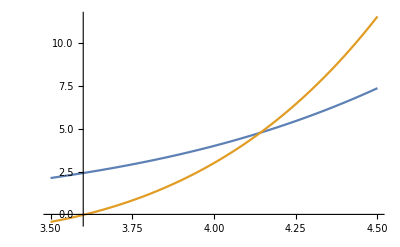

```mathematica
Plot[{-32+29 x-9 x^2+x^3,119-133 x+58 x^2-12 x^3+x^4},{x,3.5,4.5}]
```

```mathematica
Map[ChebyBaseCoeff[#]*2^Exponent[#,x]&,{-32+29 x-9 x^2+x^3,119-133 x+58 x^2-12 x^3+x^4}]
```

{{-274,118,-18,1},{2138,-1112,235,-24,1}}

```mathematica
Map[First,Select[Table[{k,Chrom[k]},{k,Range[300000,301000]}],#[[2]]==24&]]
```

{300088,300089,300090,300091,300092,300093,300094,300095,300096,300097,300100,300103,300104,300105,300106,300107,300108,300109,300110,300111,300112,300116,300117,300118,300119,300120,300121,300122,300123,300124,300125,300126,300130,300131,300132,300133,300134,300135,300136,300137,300138,300139,300142,300144,300145,300146,300147,300148,300149,300150,300151,300152,300156,300157,300158,300159,300160,300161,300162,300163,300165,300168,300169,300170,300171,300172,300173,300175,300177,300178,300179,300180,300181,300183,300186,300187,300188,300189,300191,300194,300195,300198,300199,300200,300201,300202,300203,300204,300206,300229,300230,300231,300232,300233,300234,300235,300236,300238,300257,300258,300259,300260,300261,300262,300263,300264,300265,300266,300267,300268,300269,300270,300271,300272,300275,300277,300279,300280,300281,300282,300283,300284,300285,300286,300290,300292,300293,300294,300295,300296,300297,300298,300299,300300,300303,300305,300306,300307,300308,300309,300310,300311,300312,300315,300317,300318,300319,300320,300321,300322,300323,300326,300331,300334,300335,300336,300337,300338,300339,300340,300341,300342,300343,300344,300345,300346,300347,300352,300354,300355,300356,300357,300358,300359,300360,300363,300364,300365,300366,300367,300369,300370,300371,300372,300373,300377,300378,300379,300418,300421,300422,300423,300424,300425,300426,300434,300435,300436,300437,300438,300439,300440,300442,300443,300444,300445,300446,300447,300448,300449,300450,300451,300454,300457,300459,300460,300461,300462,300463,300464,300465,300466,300471,300473,300474,300475,300476,300477,300478,300479,300480,300481,300486,300488,300489,300490,300491,300492,300493,300494,300495,300500,300502,300503,300504,300505,300506,300507,300508,300512,300513,300514,300515,300516,300517,300519,300520,300521,300525,300526,300527,300528,300532,300533,300536,300537,300538,300539,300540,300541,300542,300576,300577,300578,300579,300580,300581,300589,300590,300592,300593,300594,300595,300596,300597,300598,300599,300602,300605,300606,300607,300608,300609,300610,300611,300612,300613,300614,300615,300616,300619,300622,300623,300624,300625,300626,300627,300628,300629,300632,300635,300637,300638,300639,300640,300641,300642,300643,300644,300650,300652,300653,300654,300655,300656,300657,300658,300660,300664,300665,300666,300667,300668,300669,300671,300674,300675,300676,300678,300682,300683,300684,300685,300687,300690,300691,300694,300695,300696,300697,300698,300699,300700,300727,300729,300730,300731,300732,300733,300734,300736,300757,300758,300759,300760,300761,300762,300763,300770,300771,300772,300774,300775,300776,300777,300778,300779,300780,300781,300782,300783,300784,300785,300786,300787,300788,300789,300795,300796,300797,300798,300799,300800,300801,300802,300807,300809,300810,300811,300812,300813,300814,300815,300820,300821,300822,300823,300824,300825,300829,300830,300831,300836,300837,300838,300839,300843,300844,300847,300848,300849,300850,300851,300852,300917,300919,300920,300921,300922,300923,300924,300932,300933,300935,300936,300937,300938,300939,300940,300942,300945,300946,300947,300948,300949,300950,300951,300952,300953,300957,300958,300959,300960,300961,300962,300964,300968,300969,300970,300971,300972,300974,300977,300978,300979,300980,300981,300986,300987,300988,300989,300992,300993,300995,300996,300997,300998,301000}

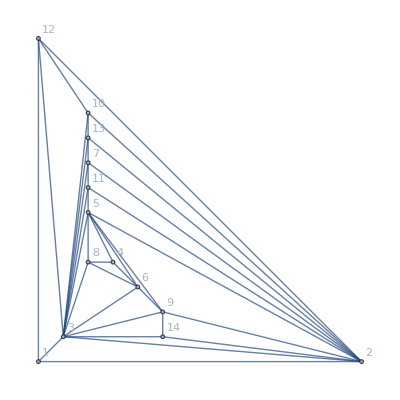

```mathematica
Graph[ReadGrof[300091], GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]
```

```mathematica
Map[First,{{300088,24},{300089,24},{300090,24},{300091,24},{300092,24},{300093,24},{300094,24},{300095,24},{300096,24},{300097,24},{300100,24}}]
```

{300088,300089,300090,300091,300092,300093,300094,300095,300096,300097,300100}

```mathematica
Tally[
Table[
With[{g=ReadGrof[k]},
{VertexDegree[g,1]+VertexDegree[g,2]+VertexDegree[g,12]-9, ChromaticPolynomial[VertexDelete[Graph[g, GraphLayout->"PlanarEmbedding", VertexLabels->"Name"],{1,2,12}],4]/24}],
{k,Map[First,Select[Table[{k,Chrom[k]},{k,Range[300000,301000]}],#[[2]]==24&]]}
]
]//Sort
```

{{{3,4},8},{{4,8},143},{{5,8},52},{{5,12},1},{{5,16},78},{{6,8},54},{{6,16},38},{{6,32},32},{{7,16},36},{{7,32},22},{{8,24},1},{{8,32},13}}